```mathematica
g[x_]:=If[x<0,Tanh[-x/2]/Tanh[1/2],Tanh[x/2]/Tanh[1/2]]
```

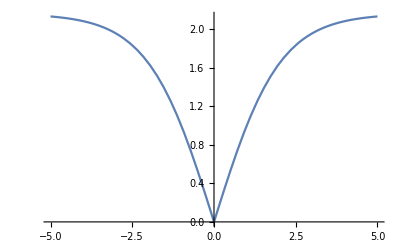

```mathematica
Plot[g[x],{x,-5,5}]
```

```mathematica
D[Tanh[x/2],x]
```

1/2 Sech[x/2]^2

```mathematica
h[x_]:=(1/2)(If[x<0,-(1/2)Sech[-x/2]^2/Tanh[1/2],(1/2)Sech[x/2]^2/Tanh[1/2]]+
                         If[x>0,(1/2)Sech[x/2]^2/Tanh[1/2],-(1/2)Sech[-x/2]^2/Tanh[1/2]])
```

```mathematica
h[x]
```

1/2 (If[x>0,Sech[x/2]^2/(2 Tanh[1/2]),-Sech[-x/2]^2/(2 Tanh[1/2])]+If[x<0,-Sech[-x/2]^2/(2 Tanh[1/2]),Sech[x/2]^2/(2 Tanh[1/2])])

```mathematica
g[x]
```

If[x<0,Tanh[-x/2]/Tanh[1/2],Tanh[x/2]/Tanh[1/2]]

```mathematica
(* BIRDOID WITH BIAS AND LEARNING ARBITRARY RATE *)
(n=1;
b=0.917305115543521;
{w1,w2}={0.5921908684844923,0.20764932665001293};
eta=0.6;
max=10;
g[x_]:= If[x<0,Tanh[-x/2]/Tanh[1/2],Tanh[x/2]/Tanh[1/2]];
h[x_]:=1/2 (If[x>0,Sech[x/2]^2/(2 Tanh[1/2]),-Sech[-x/2]^2/(2 Tanh[1/2])]+If[x<0,-Sech[-x/2]^2/(2 Tanh[1/2]),Sech[x/2]^2/(2 Tanh[1/2])]);
Label[1];
x1=RandomInteger[];
x2=RandomInteger[];
n=n+1;
b=b-eta(-(g[x1-x2]-g[b+w1 x1+w2 x2]))h[b+w1 x1+w2 x2];
w1=w1-eta(-x1(g[x1-x2]-g[b+w1 x1+w2 x2]))h[b+w1 x1+w2 x2];
w2=w2-eta(-x2(g[x1-x2]-g[b+w1 x1+w2 x2]))h[b+w1 x1+w2 x2];
If[n<max,Goto [1]];
Print[{(g[x1-x2]-g[b+w1 x1+w2 x2])^2/4,b,{x1,x2},{w1,w2},g[b+w1 x1+w2 x2],UnitStep[g[b+w1 x1+w2 x2]-1/2],max}];
)
```

{6.71831×10^-7,0.0991894,{1,1},{-0.0695142,-0.0281601},0.00163931,0,10}

{0.044117,-0.393243,{0,0},{0.132435,0.0277135},0.420081,0,10}

{0.00386617,0.833968,{0,1},{0.53868,0.0244254},0.875643,1,10}

{0.0000995765,0.412908,{1,0},{0.563763,0.388643},0.980042,1,10}

{0.0240297,-0.288526,{0,0},{-0.241755,-0.0282682},0.31003,0,10}

{0.0000205019,-0.310214,{1,1},{0.151485,0.167099},0.0090558,0,10}

{0.000425388,0.130518,{1,1},{-0.0228029,-0.0695862},0.0412499,0,10}

{6.58721×10^-7,-0.0497183,{1,1},{0.0359393,0.0152792},0.00162323,0,10}

{0.00114399,-0.062541,{0,0},{0.08177,-0.283593},0.0676459,0,10}

{0.00332687,-0.808001,{0,1},{0.0043072,-0.0603582},0.884642,1,10}

{0.00175741,0.0775294,{0,0},{-0.0891463,-0.159422},0.0838431,0,10}

{0.00152481,0.451614,{1,0},{0.458451,0.214586},0.921902,1,10}

{0.0000328757,0.674971,{1,0},{0.311595,0.0877678},0.988533,1,10}

{0.014274,0.221748,{0,0},{0.0749761,0.25415},0.238948,0,10}

{0.00166392,1.13014,{1,0},{-0.224011,0.0599431},0.918418,1,10}

{0.0693834,0.496877,{0,0},{0.164338,-0.0584758},0.526815,1,10}

{0.000292318,-0.706458,{1,0},{-0.253721,-0.379608},0.965805,1,10}

{1.30293×10^-10,0.680338,{0,1},{0.592191,0.319635},0.999977,1,10}

{0.00352614,0.0180959,{1,1},{-0.0487047,0.140484},0.118763,0,10}

{0.000367701,-0.739381,{0,1},{0.0373549,-0.216006},0.961649,1,10}

{0.000761996,0.527271,{1,1},{-0.313882,-0.162353},0.0552086,0,10}

{0.0000154107,0.0729,{1,1},{0.152402,-0.218045},0.0078513,0,10}

{0.000201521,-0.026242,{0,0},{0.366922,-0.303284},0.0283916,0,10}

{0.00213391,0.703303,{1,0},{0.19068,-0.0257657},0.907611,1,10}

{0.000380981,-0.0149356,{1,1},{0.139687,-0.0886676},0.0390375,0,10}

{0.00209189,0.468062,{0,1},{0.592191,0.426946},0.908526,1,10}

{0.0000248715,0.962783,{0,1},{-0.00666821,0.0255266},0.990026,1,10}

{0.00655786,0.149971,{0,0},{-0.118284,-0.250672},0.161961,0,10}

{0.000325081,0.851411,{0,1},{0.247622,0.106616},0.96394,1,10}

{0.000258656,0.617767,{1,0},{0.344755,-0.319417},0.967834,1,10}

{0.0135668,0.216141,{0,0},{0.529918,0.292027},0.232953,0,10}

{0.00371913,0.626362,{1,0},{0.234671,-0.0257657},0.878031,1,10}

{2.391×10^-7,-0.354621,{1,1},{0.390009,-0.0362918},0.000977957,0,10}

{0.000286063,0.858897,{0,1},{0.529016,0.101706},0.966173,1,10}

{0.000430939,-0.198133,{1,1},{0.352966,-0.193211},0.0415181,0,10}

{0.0333353,0.340752,{0,0},{0.342736,0.12151},0.365159,0,10}

{0.00380059,0.319381,{1,0},{0.540183,0.0507364},0.876702,1,10}

{1.07953×10^-6,0.305761,{1,0},{0.691798,0.290849},0.997922,1,10}

{0.000614532,0.0458311,{0,0},{-0.191257,-0.0827244},0.0495795,0,10}

{1.94761×10^-7,0.226381,{1,1},{0.04265,-0.268216},0.000882635,0,10}

{4.23978×10^-6,0.856905,{1,0},{0.14794,0.0460085},1.00412,1,10}

{0.00484389,0.813859,{0,1},{-0.0058641,0.0281879},0.860804,1,10}

{0.00459956,0.823671,{0,1},{-0.0804092,0.0222834},0.86436,1,10}

{0.011302,0.197148,{0,0},{0.542765,0.273901},0.212621,0,10}

{0.00203567,0.614831,{1,0},{0.281566,0.098655},0.909763,1,10}

{0.00366816,-1.10412,{1,0},{0.242161,-0.268662},0.878869,1,10}

{5.47515×10^-13,-0.0491745,{1,1},{-0.00954146,0.0587174},1.47988×10^-6,0,10}

{1.61033×10^-7,-0.161728,{1,1},{-0.0213915,0.182378},0.000802579,0,10}

{0.0579719,0.452635,{0,0},{-0.23466,0.0430332},0.481547,0,10}

{8.65927×10^-8,-0.00177419,{1,1},{-0.172772,0.17509},0.000588533,0,10}

{0.0000642863,0.689182,{1,0},{0.292054,0.305842},0.983964,1,10}

{0.00145033,-0.961755,{1,0},{0.0495083,-0.090415},0.923834,1,10}

{0.0000339629,1.01755,{1,0},{-0.0312092,-0.00755209},0.988344,1,10}

{0.000196399,1.02664,{0,1},{0.19792,-0.0593313},0.971972,1,10}

{0.0190548,0.256559,{0,0},{0.23873,0.0589701},0.276078,0,10}

{0.0045392,0.554146,{0,1},{0.0488052,0.29279},0.865253,1,10}

{2.14273×10^-7,-0.0256993,{1,1},{0.064158,-0.0376031},0.000925793,0,10}

{0.000329845,0.148724,{1,1},{0.00332656,-0.118477},0.0363232,0,10}

{0.00313679,0.475451,{1,0},{0.396621,-0.0718189},0.887986,1,10}

{0.00502443,-0.742719,{1,0},{-0.0965068,0.166445},0.858234,1,10}

{0.0041272,0.692992,{0,1},{0.388866,0.160841},0.871513,1,10}

{0.0000235677,-0.3556,{1,1},{0.289663,0.0749113},0.00970932,0,10}

{0.000381061,0.69163,{0,1},{-0.000293148,0.262962},0.960958,1,10}

{0.00481633,-0.725233,{1,0},{-0.11725,0.0671997},0.8612,1,10}

{0.00778971,0.0674309,{1,1},{0.0983862,-0.00230915},0.176519,0,10}

{0.000325985,0.486798,{1,0},{0.471171,0.14201},0.96389,1,10}

{0.00321429,0.729279,{1,0},{0.141266,0.207806},0.886611,1,10}

{0.000279672,0.418226,{1,0},{0.542817,-0.0396632},0.966553,1,10}

{0.0000961451,0.0147742,{1,1},{-0.0110158,0.014367},0.0196107,0,10}

{0.000709503,-0.473667,{1,1},{0.301357,0.123063},0.053273,0,10}

{0.00376428,-0.885639,{1,0},{0.0254226,-0.472469},0.877292,1,10}

{0.00369534,-0.0860479,{1,1},{0.121884,0.0766493},0.121579,0,10}

{0.0000847714,0.8586,{0,1},{0.203644,0.119867},0.981586,1,10}

{0.0049154,-0.413404,{1,0},{-0.427519,0.0289487},0.85978,1,10}

{0.00779022,0.163513,{0,0},{-0.326353,-0.116435},0.176524,0,10}

{0.00373012,-0.25651,{0,1},{0.204532,-0.604324},0.877851,1,10}

{0.0468445,0.405543,{0,0},{0.0364388,0.216924},0.432872,0,10}

{0.00333275,0.432993,{1,0},{0.435253,-0.292088},0.88454,1,10}

{0.000312431,-0.566358,{0,1},{0.16636,-0.392487},0.964649,1,10}

{0.000985197,-0.292312,{1,1},{0.178805,0.171542},0.0627757,0,10}

{0.0170023,0.242204,{0,0},{-0.316315,0.244149},0.260786,0,10}

{3.44121×10^-6,0.961659,{0,1},{0.278998,0.0339857},0.99629,1,10}

{0.0000951477,0.907238,{1,0},{0.0699554,0.255783},0.980491,1,10}

{0.0421158,-0.383995,{0,0},{0.179496,-0.0212821},0.410443,0,10}

{2.86215×10^-6,0.616249,{0,1},{0.592191,0.379778},0.996616,1,10}

{0.000696244,0.0487842,{0,0},{-0.0283224,-0.0215602},0.0527729,0,10}

{0.00531301,-0.13494,{0,0},{-0.102137,-0.378322},0.145781,0,10}

{0.00405224,-0.801369,{0,1},{0.169679,-0.0537583},0.872686,1,10}

{0.0001802,0.202014,{1,1},{0.0659604,-0.243159},0.0268477,0,10}

{2.67776×10^-7,0.0149921,{1,1},{0.0804861,-0.0945217},0.00103494,0,10}

{0.000677311,-0.161796,{1,1},{0.218353,-0.00844062},0.0520504,0,10}

{0.000208525,0.0266942,{0,0},{-0.150725,-0.121116},0.0288808,0,10}

{0.00022119,-0.779854,{0,1},{0.348045,-0.185467},0.970255,1,10}

{0.00326384,0.566392,{0,1},{0.497147,0.303186},0.88574,1,10}

{0.00138727,0.480509,{1,0},{0.433631,0.271444},0.925508,1,10}

{0.000103116,0.818629,{1,0},{0.157633,0.227021},0.979691,1,10}

{0.00111864,0.891924,{0,1},{0.113839,0.0308284},0.933108,1,10}

{0.000997909,0.0584092,{0,0},{-0.0072844,-0.140164},0.0631794,0,10}

{0.0050905,-0.710076,{1,0},{-0.128131,0.0858224},0.857305,1,10}

{0.00353779,0.375631,{1,0},{0.488736,-0.303066},0.881041,1,10}

{0.00340521,0.715008,{0,1},{-0.235321,0.151853},0.883292,1,10}

{0.0000275915,0.799078,{1,0},{0.18861,-0.219011},0.989494,1,10}

{0.000895774,0.0553378,{0,0},{-0.0500503,-0.0933041},0.059859,0,10}

{0.000100573,-0.0185381,{0,0},{-0.000208497,0.0624916},0.0200573,0,10}

{0.00600776,0.14352,{0,0},{-0.407779,0.00321416},0.155019,0,10}

{0.00711668,-0.156255,{0,0},{0.0660342,-0.131701},0.168721,0,10}

{0.00422824,0.987539,{0,1},{0.429286,-0.135429},0.86995,1,10}

{0.00460589,0.59501,{1,0},{0.250842,-0.194219},0.864267,1,10}

{0.000129325,0.325354,{1,1},{0.00559738,-0.30993},0.0227443,0,10}

{0.000206328,-0.0265532,{0,0},{0.162084,0.118955},0.0287283,0,10}

{7.57276×10^-8,-0.162362,{1,1},{-0.0602164,0.223087},0.000550373,0,10}

{0.000302195,0.1784,{1,1},{-0.00737569,-0.138888},0.0347675,0,10}

{0.000386213,0.174412,{1,1},{-0.0295289,-0.108552},0.0393046,0,10}

{0.00201862,0.901076,{0,1},{0.215947,-0.0042533},0.910142,1,10}

{0.000420794,0.0379227,{0,0},{0.112665,-0.238526},0.0410265,0,10}

{0.0489258,-0.414709,{0,0},{0.0428109,0.174961},0.442384,0,10}

{0.000103461,0.0688533,{1,1},{-0.0352023,-0.0148486},0.0203431,0,10}

{0.0415327,0.381262,{0,0},{-0.121385,0.000529836},0.407591,0,10}

{0.020471,0.266031,{0,0},{0.0695386,0.281743},0.286154,0,10}

{0.000566643,-1.062,{0,1},{0.00320745,0.117248},0.952391,1,10}

{0.0000862108,0.582379,{1,0},{0.395906,0.347861},0.98143,1,10}

{4.74711×10^-6,0.00402742,{0,0},{-0.0447993,0.102771},0.00435757,0,10}

{3.45389×10^-7,0.423797,{1,1},{-0.349297,-0.0734138},0.0011754,0,10}

{0.0571807,0.44943,{0,0},{0.0531133,-0.0261719},0.47825,0,10}

{0.000122941,0.0204963,{0,0},{-0.088625,0.039191},0.0221757,0,10}

{0.00139529,1.02433,{1,0},{-0.110428,0.046414},0.925293,1,10}

{0.00832104,0.169018,{0,0},{-0.0415067,-0.147786},0.182439,0,10}

{0.00149573,-0.693934,{0,1},{-0.371643,-0.216976},0.922651,1,10}

{0.00500405,-0.809294,{1,0},{-0.0302475,-0.360517},0.858521,1,10}

{0.00154573,-0.800113,{1,0},{-0.109349,-0.254437},0.921368,1,10}

{5.2454×10^-9,-0.929134,{1,0},{-0.0710364,0.00413918},1.00014,1,10}

{0.00432538,-0.516665,{1,0},{-0.333807,0.184822},0.868465,1,10}

{0.000213674,-0.449704,{0,1},{0.0765555,-0.516206},0.970765,1,10}

{0.00242575,0.768564,{0,1},{0.166997,0.118571},0.901496,1,10}

{0.00659728,-0.150422,{0,0},{-0.400517,0.0385133},0.162447,0,10}

{6.89129×10^-7,0.0905202,{1,1},{-0.259488,0.170502},0.00166028,0,10}

{0.00397589,0.846276,{0,1},{-0.129596,0.0101812},0.873891,1,10}

{0.0000217148,0.808408,{1,0},{0.202572,-0.0703784},1.00932,1,10}

{0.0000748047,0.0159877,{0,0},{0.156973,-0.210542},0.0172979,0,10}

{0.00052276,-0.220417,{1,1},{0.327337,-0.14919},0.0457279,0,10}

{0.000432035,0.841787,{1,0},{0.207635,-0.0427213},1.04157,1,10}

{0.0341313,-0.344877,{0,0},{-0.154433,-0.476987},0.369493,0,10}

{0.00123561,0.363302,{1,1},{-0.234753,-0.0635495},0.0703025,0,10}

{0.000514637,0.0419398,{0,0},{0.0824424,-0.023481},0.0453712,0,10}

{0.00207396,0.481888,{0,1},{0.458126,0.413562},0.908918,1,10}

{0.000723651,0.920403,{0,1},{-0.0983378,0.143784},1.0538,1,10}

{0.00149699,0.73997,{0,1},{0.311244,0.170904},0.922618,1,10}

{0.00152232,0.362229,{1,1},{-0.146807,-0.143269},0.0780339,0,10}

{0.0057957,0.140956,{0,0},{-0.0976047,0.0505822},0.152259,0,10}

{0.000614751,0.574697,{0,1},{0.524154,0.367785},0.950412,1,10}

{0.00108452,-0.949842,{0,1},{0.0537006,-0.129012},1.06586,1,10}

{0.00441628,-0.465809,{1,0},{-0.38315,-0.117164},0.86709,1,10}

{0.000432494,-0.318077,{1,1},{0.266765,0.0128655},0.041593,0,10}

{0.00357302,0.218256,{1,1},{-0.0788972,-0.0287544},0.119549,0,10}

{0.0249399,0.294017,{0,0},{0.354195,0.111383},0.315848,0,10}

{0.0000279473,0.899983,{0,1},{0.528794,0.0876265},0.989427,1,10}

{4.76296×10^-6,1.02012,{0,1},{0.127301,-0.025246},0.995635,1,10}

{0.0000183723,-0.00792312,{0,0},{0.193343,0.0903928},0.00857258,0,10}

{0.000105023,0.986721,{0,1},{0.0729321,-0.0106763},0.979504,1,10}

{0.00152091,-0.0253177,{1,1},{-0.0868947,0.184332},0.0779978,0,10}

{0.000890341,0.632296,{0,1},{0.499444,0.298663},0.940323,1,10}

{0.00162664,0.0745862,{0,0},{0.074473,0.213828},0.0806632,0,10}

{1.16808×10^-6,-0.309275,{1,1},{0.186935,0.124338},0.00216156,0,10}

{0.0000804811,-0.0165832,{0,0},{0.140186,-0.08121},0.0179423,0,10}

{5.22518×10^-6,-0.113115,{1,1},{0.0563391,0.0610017},0.00457173,0,10}

{0.0000513986,1.00176,{0,1},{-0.136123,-0.0185472},0.985661,1,10}

{0.00178412,-1.00829,{1,0},{0.105418,-0.191165},0.915522,1,10}

{0.000439251,0.741598,{1,0},{0.30824,0.12151},1.04192,1,10}

{0.00168451,0.274106,{1,0},{0.63146,0.199324},0.917915,1,10}

{0.0000139313,0.893198,{0,1},{0.233049,0.098047},0.992535,1,10}

{0.00487481,-0.0727471,{1,1},{0.0575882,0.144398},0.13964,0,10}

{7.3935×10^-6,0.507555,{1,0},{0.498845,0.427211},1.00544,1,10}

{0.00336713,0.724029,{0,1},{-0.242855,0.143557},0.883946,1,10}

{0.0000276043,-0.939384,{1,0},{-0.0730006,-0.0325998},1.01051,1,10}

{0.00217421,0.694586,{1,0},{0.417976,0.206803},1.09326,1,10}

{0.0000466854,0.187084,{1,1},{-0.0733601,-0.101094},0.0136653,0,10}

{0.0606541,0.463358,{0,0},{-0.00477939,-0.233458},0.492561,0,10}

{0.000088992,0.0174381,{0,0},{0.0160594,-0.171222},0.0188671,0,10}

{1.87033×10^-6,0.81985,{1,0},{0.176938,-0.0326398},0.997265,1,10}

{0.000156824,0.700511,{0,1},{0.348841,0.270252},0.974954,1,10}

{0.00478941,0.617786,{0,1},{-0.0488822,0.225122},0.861589,1,10}

{0.004077,-0.989027,{1,0},{0.134329,0.000858224},0.872297,1,10}

{0.00509555,0.647221,{1,0},{0.190909,0.0887264},0.857234,1,10}

{0.0449958,-0.397244,{0,0},{0.0377108,0.032645},0.424244,0,10}

{0.0000113084,0.492156,{1,0},{0.499955,0.464589},0.993274,1,10}

{0.000169235,0.0240479,{0,0},{-0.104565,-0.152406},0.0260181,0,10}

{0.0000102106,-0.171077,{1,1},{0.126879,0.0501045},0.0063908,0,10}

{0.000288754,0.202451,{1,1},{-0.0248626,-0.146175},0.0339855,0,10}

{0.000605341,0.554199,{1,0},{0.50443,0.27937},1.04921,1,10}

{0.000318279,0.0480505,{1,1},{0.278241,-0.359272},0.0356807,0,10}

{0.00469378,0.522126,{0,1},{-0.0627487,0.322308},0.862978,1,10}

{0.000047527,1.02428,{0,1},{0.113909,-0.0404261},0.986212,1,10}

{0.00313676,0.45578,{1,0},{0.416293,-0.330344},0.887986,1,10}

{2.04607×10^-9,0.0000836127,{0,0},{0.0686716,0.0471424},0.000090467,0,10}

{0.00850204,-0.170855,{0,0},{0.124738,-0.369559},0.184413,0,10}

{4.7768×10^-7,0.416654,{1,1},{-0.334465,-0.0809122},0.00138229,0,10}

{0.0602772,0.461864,{0,0},{0.109847,-0.0572785},0.491028,0,10}

{0.000223783,0.0258052,{1,1},{0.200865,-0.199016},0.0299188,0,10}

{0.00130797,-0.884261,{1,0},{-0.0323234,-0.143273},0.927668,1,10}

{0.00112902,0.247703,{1,1},{-0.133963,-0.0516096},0.0672019,0,10}

{4.54072×10^-8,0.106577,{1,1},{-0.0376974,-0.0684858},0.000426179,0,10}

{0.00161718,0.68689,{0,1},{0.395762,0.220544},0.919572,1,10}

{0.00592191,0.142488,{0,0},{0.0292477,0.151583},0.153908,0,10}

{0.0000213443,0.651394,{0,1},{0.715769,0.337774},0.99076,1,10}

{0.000161711,0.138593,{1,1},{0.151363,-0.266448},0.0254331,0,10}

{0.00283355,0.0984756,{0,0},{0.120696,0.112938},0.106462,0,10}

{0.0000132011,0.0821063,{1,1},{0.149136,-0.224526},0.00726667,0,10}

{0.0000677378,-0.0894645,{1,1},{-0.112168,0.216847},0.0164606,0,10}

{0.0041176,-0.289412,{1,1},{-0.0233742,0.194034},0.128337,0,10}

{8.14541×10^-6,-0.220837,{1,1},{0.0955997,0.130513},0.00570803,0,10}

{0.00330582,0.642228,{1,0},{0.226537,0.271972},0.885007,1,10}

{0.000237478,0.0284874,{0,0},{0.0308169,-0.127943},0.0308206,0,10}

{0.0000215196,0.518158,{1,0},{0.492773,0.34056},1.00928,1,10}

{0.00367508,0.686868,{0,1},{-0.179815,0.174967},0.878755,1,10}

{0.000594585,0.0450809,{0,0},{0.429446,-0.292166},0.0487682,0,10}

{0.000215442,1.02159,{0,1},{0.340802,-0.0558216},0.970644,1,10}

{0.000131358,0.941264,{0,1},{0.154613,0.0319631},0.977078,1,10}

{0.000678968,0.321298,{1,1},{-0.324579,0.0514562},0.052114,0,10}

{0.00460003,0.945496,{0,1},{0.145805,-0.0995498},0.864353,1,10}

{0.0000154285,0.468628,{1,0},{0.522159,0.00880119},0.992144,1,10}

{0.000151263,0.480425,{0,1},{0.599579,0.490857},0.975402,1,10}

{0.0774694,-0.526312,{0,0},{0.0279259,0.123371},0.556666,1,10}

{0.003944,-0.727764,{0,1},{0.270367,-0.129253},0.874397,1,10}

{0.000267412,-0.153224,{1,1},{0.341461,-0.158007},0.0327055,0,10}

{0.0000149118,0.189113,{1,1},{-0.039268,-0.142707},0.00772315,0,10}

{0.0000125218,-0.313743,{1,1},{0.321917,-0.00163263},0.00707724,0,10}

{0.0000358715,-1.0694,{0,1},{0.113829,0.0834345},0.988021,1,10}

{0.000208218,0.676904,{0,1},{-0.0598214,0.289441},0.97114,1,10}

{2.59008×10^-11,0.0950483,{1,1},{-0.0388075,-0.0562314},0.0000101786,0,10}

{0.00224228,-0.8612,{0,1},{0.451198,-0.0301855},0.905295,1,10}

{0.000338983,-0.477347,{0,1},{0.131297,-0.4798},0.963177,1,10}

{0.0202716,0.264717,{0,0},{0.18373,0.283807},0.284757,0,10}

{0.00294451,1.05269,{1,0},{-0.176742,0.182026},0.891473,1,10}

{0.00283629,-0.0985232,{0,0},{0.216123,-0.210018},0.106514,0,10}

{0.00115333,-0.447133,{1,1},{0.312868,0.19706},0.0679214,0,10}

{0.0000204873,-0.113482,{1,1},{0.178748,-0.0736328},0.00905257,0,10}

{0.00480334,0.525802,{1,0},{0.316886,-0.15667},0.861388,1,10}

{0.000402306,0.283995,{1,1},{-0.018852,-0.228063},0.0401151,0,10}

{0.00501366,0.731033,{0,1},{0.223066,0.10836},0.858386,1,10}

{0.0138863,0.218691,{0,0},{0.48069,0.333027},0.23568,0,10}

{0.0000450381,-0.586604,{1,1},{0.583074,-0.00887567},0.0134221,0,10}

{0.0128968,-0.210695,{0,0},{0.277291,-0.303715},0.227128,0,10}

{0.000443924,0.0389513,{0,0},{-0.280851,-0.000240324},0.042139,0,10}

{0.0738784,-0.513413,{0,0},{0.116741,-0.0200752},0.543612,1,10}

{0.00231368,0.665242,{1,0},{0.224468,0.0511139},0.903799,1,10}

{0.000192689,0.58536,{1,0},{0.382255,0.0464286},0.972238,1,10}

{0.0000836419,0.180047,{1,1},{0.17111,-0.368062},0.0182912,0,10}

{0.00461551,0.984613,{1,0},{-0.138917,-0.022055},0.864125,1,10}

{0.00032697,0.583179,{1,1},{-0.420169,-0.129583},0.0361646,0,10}

{0.000032804,-1.03945,{0,1},{0.0986252,0.052869},0.988545,1,10}

{0.0276371,0.30975,{0,0},{0.161914,0.115002},0.332488,0,10}

{0.000323247,-0.305816,{1,1},{0.392337,-0.119759},0.0359582,0,10}

{0.000397434,-0.0368548,{0,0},{0.0783578,0.131411},0.0398715,0,10}

{0.00472959,0.633573,{0,1},{0.0700803,0.210288},0.862456,1,10}

{0.00021359,0.26104,{1,1},{0.0838312,-0.317855},0.0292295,0,10}

{1.27089×10^-9,-0.034912,{1,1},{0.161679,-0.126833},0.0000712991,0,10}

{0.00458615,0.573248,{1,0},{0.272924,-0.0832994},0.864558,1,10}

{0.00395815,-0.669824,{0,1},{0.177748,-0.186944},0.874172,1,10}

{0.000160744,-0.454647,{0,1},{0.0136663,-0.515755},0.974643,1,10}

{0.00285567,0.788147,{1,0},{0.0896416,-0.233458},0.893123,1,10}

{0.000301892,-0.401689,{1,1},{0.238106,0.131463},0.0347501,0,10}

{0.00509919,0.255299,{1,0},{0.582775,-0.0442004},0.857183,1,10}

{0.0000476335,-0.361993,{1,1},{0.318923,0.0303118},0.0138034,0,10}

{0.00112455,0.306554,{1,1},{-0.160948,-0.0835994},0.0670685,0,10}

{0.0000290233,0.848287,{1,0},{0.139087,-0.147423},0.989225,1,10}

{0.00320092,0.104676,{0,0},{-0.203571,-0.121648},0.113153,0,10}

{0.00451283,-1.02763,{1,0},{0.180266,0.128654},0.865645,1,10}

{2.39637×10^-6,-0.125485,{1,1},{0.00454962,0.123797},0.00309604,0,10}

{0.0105379,0.190326,{0,0},{0.598406,0.334013},0.205308,0,10}

{0.0000135858,0.532326,{0,1},{0.473333,0.459028},0.992628,1,10}

{0.000770835,-0.282837,{1,1},{0.0929519,0.241217},0.0555278,0,10}

{0.0979832,0.595618,{0,0},{-0.282059,-0.0336999},0.626045,1,10}

{0.000312061,-0.0118307,{1,1},{0.281798,-0.302624},0.0353305,0,10}

{0.000349587,0.657084,{0,1},{-0.0598682,0.299405},0.962605,1,10}

{0.0000466849,-0.0209627,{1,1},{0.0867454,-0.0531526},0.0136653,0,10}

{1.15465×10^-15,0.117181,{1,1},{-0.0920695,-0.0251114},6.79603×10^-8,0,10}

{1.05437×10^-7,-0.513899,{1,1},{0.393991,0.119308},0.000649422,0,10}

{0.0642421,0.477377,{0,0},{0.176728,0.00874084},0.506921,1,10}

{0.0000384951,-0.012025,{1,1},{0.240258,-0.216764},0.0124089,0,10}

{0.0279844,0.311722,{0,0},{0.337078,0.13787},0.334571,0,10}

{0.00138072,-0.0687125,{0,0},{0.220458,0.0147036},0.0743161,0,10}

{0.000811852,0.245335,{1,1},{-0.272784,0.0801293},0.056986,0,10}

{0.0276604,0.309882,{0,0},{-0.0267321,0.0963947},0.332628,0,10}

{7.54077×10^-7,0.49685,{1,0},{0.505192,0.305594},1.00174,1,10}

{0.00657983,0.150222,{0,0},{0.190551,0.0197986},0.162232,0,10}

{0.0252585,0.295916,{0,0},{-0.0156125,0.262103},0.317858,0,10}

{0.00438331,-0.543659,{1,0},{-0.305847,0.137975},0.867587,1,10}

{0.0612624,0.46576,{0,0},{-0.0382843,0.0141295},0.495025,0,10}

{0.000448276,-0.0391417,{0,0},{0.0681582,0.0616562},0.042345,0,10}

{6.15733×10^-6,-0.00458679,{0,0},{0.12528,0.0707016},0.00496279,0,10}

{0.000859837,-0.360489,{1,1},{0.231608,0.0746653},0.058646,0,10}

{0.000294087,0.448941,{1,0},{0.511119,-0.0320072},0.965702,1,10}

{0.000190127,-0.686122,{0,1},{0.364128,-0.281707},0.972423,1,10}

{0.0000504367,0.955162,{1,0},{0.0282097,-0.0917856},0.985796,1,10}

{0.0000209727,0.129403,{1,1},{-0.148825,0.0109568},0.00915919,0,10}

{0.0000442216,-0.493818,{1,1},{0.582447,-0.100921},0.0132999,0,10}

{0.000331088,0.787245,{1,0},{0.1704,-0.0139916},0.963608,1,10}

{0.00511995,0.66621,{0,1},{-0.0526457,0.171545},0.856892,1,10}

{0.0000732026,0.0158156,{0,0},{0.118363,-0.16264},0.0171117,0,10}

{0.00409603,-0.465874,{1,0},{-0.388496,0.0136034},0.872,1,10}

{0.000381006,-0.458194,{0,1},{0.0354516,-0.496401},0.960961,1,10}

{0.000552778,-0.938497,{0,1},{0.0452821,-0.117493},1.04702,1,10}

{0.000510838,-0.0417847,{0,0},{0.20414,-0.064773},0.0452035,0,10}

{0.000107302,0.0191483,{0,0},{0.142452,-0.351194},0.0207173,0,10}

{0.00260961,-0.78012,{1,0},{-0.102919,-0.417262},0.897831,1,10}

{0.00209245,0.0846055,{0,0},{-0.0641716,0.162581},0.0914867,0,10}

{0.00511995,0.66621,{0,1},{-0.0526457,0.171545},0.856892,1,10}

{0.00320755,0.104784,{0,0},{0.520023,-0.10298},0.11327,0,10}

{0.00400104,-0.117056,{0,0},{-0.215252,-0.0907913},0.126508,0,10}

{0.0000835812,0.972057,{0,1},{0.0609029,0.00656043},0.981715,1,10}

{0.0666954,-0.486764,{0,0},{0.0407087,0.0614092},0.516509,1,10}

{0.00135172,0.346027,{1,1},{-0.0972228,-0.180817},0.0735316,0,10}

{0.000022281,0.784649,{1,0},{0.226474,0.160764},1.00944,1,10}

{0.00374353,-0.821561,{1,0},{-0.0390302,0.287494},0.877631,1,10}

{2.78798×10^-7,0.0422158,{1,1},{0.16497,-0.208162},0.00105603,0,10}

{0.0000696082,-0.405739,{1,1},{0.517306,-0.126989},0.0166863,0,10}

{4.36375×10^-7,0.00122107,{0,0},{0.106649,0.0350538},0.00132117,0,10}

{4.0391×10^-6,0.417119,{1,0},{0.58761,0.47492},1.00402,1,10}

{0.00026575,0.522033,{1,0},{0.439983,-0.364581},0.967396,1,10}

{0.000925232,0.0562408,{0,0},{0.513975,0.262146},0.0608353,0,10}

{4.50468×10^-9,1.02937,{1,0},{-0.0295236,-0.0429172},0.999866,1,10}

{0.00117858,-0.934456,{0,1},{-0.204062,0.0137114},0.931339,1,10}

{0.000170252,-0.0241201,{0,0},{0.0827018,0.0744646},0.0260961,0,10}

{0.00478172,-0.683054,{0,1},{0.220199,-0.159977},0.8617,1,10}

{0.00470517,0.620313,{0,1},{0.0163055,0.223939},0.862812,1,10}

{0.000315775,-0.148807,{1,1},{0.0887054,0.0929515},0.0355401,0,10}

{0.000875652,-0.013348,{1,1},{-0.147577,0.215638},0.0591828,0,10}

{5.64749×10^-11,-0.276865,{1,1},{0.200391,0.076488},0.00001503,0,10}

{0.00571418,0.139958,{0,0},{-0.279222,-0.136544},0.151184,0,10}

{0.00354832,0.375861,{1,0},{0.48831,-0.296579},0.880864,1,10}

{0.00506304,-0.334406,{1,0},{-0.504224,0.012812},0.85769,1,10}

{0.00398236,0.563724,{1,0},{0.29262,-0.260817},0.873788,1,10}

{5.85072×10^-7,0.520267,{1,0},{0.477936,0.411629},0.99847,1,10}

{0.00426901,0.458833,{1,0},{0.392587,-0.141169},0.869325,1,10}

{0.0284898,0.31457,{0,0},{0.217292,0.191628},0.337579,0,10}

{6.47873×10^-6,0.54777,{0,1},{0.467842,0.446255},0.994909,1,10}

{0.0631072,0.472981,{0,0},{0.0846459,0.0102783},0.502423,1,10}

{0.00308735,0.102799,{0,0},{-0.083102,0.12001},0.111128,0,10}

{0.000328173,0.850762,{1,0},{0.107067,-0.0909738},0.963769,1,10}

{1.66003×10^-6,0.907479,{1,0},{0.0894953,0.125918},0.997423,1,10}

{0.00027234,-1.09762,{1,0},{0.136072,-0.297176},0.966995,1,10}

{0.00505455,0.605212,{1,0},{0.233549,0.0681338},0.857809,1,10}

{0.000127853,0.775343,{1,0},{0.198241,0.107347},0.977386,1,10}

{0.00190694,-0.597875,{0,1},{0.525283,-0.30178},0.912663,1,10}

{0.0000298244,-0.779948,{0,1},{0.161739,-0.207254},0.989078,1,10}

{0.000324814,0.266644,{1,1},{-0.280041,0.0467149},0.0360452,0,10}

{0.00168534,0.0759214,{0,0},{-0.148085,-0.0556591},0.0821058,0,10}

{1.46301×10^-6,-0.146639,{1,1},{0.323423,-0.17902},0.0024191,0,10}

{0.0046708,-0.565166,{0,1},{0.0703547,-0.279638},0.863314,1,10}

{0.00248695,-0.782193,{0,1},{-0.390024,-0.103561},0.900261,1,10}

{4.08917×10^-7,0.110422,{1,1},{-1.01234,0.900739},0.00127893,0,100}

{3.39503×10^-6,0.320848,{1,1},{-0.376788,0.0593464},0.00368512,0,100}

{0.000178075,0.542652,{1,0},{0.426206,0.18542},0.973311,1,100}

{6.74753×10^-8,0.00975898,{1,1},{0.97731,-0.987549},0.00051952,0,100}

{2.7495×10^-8,0.00703574,{1,1},{0.98721,-0.994552},0.000331632,0,100}

{9.04307×10^-6,-0.228543,{1,1},{0.871401,-0.637299},0.00601434,0,100}

{4.02246×10^-7,0.00117235,{0,0},{0.993822,-0.992224},0.00126846,0,100}

{0.0000143073,-0.0124977,{0,1},{0.971596,-0.97863},0.992435,1,100}

{0.000106347,0.00933876,{1,0},{-0.985234,0.917139},0.979375,1,100}

{3.04632×10^-6,0.010532,{0,1},{0.947173,-1.00643},0.996509,1,100}

{0.000217654,0.000323562,{0,1},{0.882495,-0.96592},0.970494,1,100}

{8.2335×10^-7,0.0663508,{1,1},{-1.01357,0.945539},0.00181477,0,100}

{0.00139585,-0.0504648,{1,0},{-0.863415,0.630125},0.925278,1,100}

{8.91825×10^-8,-0.0235746,{1,1},{1.00125,-0.977119},0.000597269,0,100}

{0.0022495,-0.112208,{1,0},{-0.779007,0.736718},0.905142,1,100}

{0.00010625,-0.0298878,{0,1},{0.984758,-0.946018},0.979384,1,100}

{1.1914×10^-6,-0.0604145,{1,1},{1.00869,-0.946256},0.00218302,0,100}

{5.51234×10^-14,0.0136823,{1,1},{-0.954771,0.941089},4.69568×10^-7,0,100}

{5.99237×10^-7,0.0608133,{1,1},{-1.00368,0.941436},0.00154821,0,100}

{3.76381×10^-6,0.00863189,{0,1},{-1.00068,0.986813},0.99612,1,100}

{1.69618×10^-8,-0.00138627,{1,1},{-0.968896,0.970042},0.000260475,0,100}

{0.000944566,0.0568257,{0,0},{-0.972718,0.786788},0.0614676,0,100}

{0.00124626,-0.847855,{1,0},{-0.236792,-0.0375661},1.0706,1,100}

{0.0000216957,-0.0206587,{0,1},{1.00082,-0.968421},0.990684,1,100}

{5.04161×10^-6,0.00415047,{0,0},{0.98767,-1.04463},0.00449071,0,100}

{0.0027998,-0.498994,{0,1},{0.363904,-0.379965},0.894174,1,100}

{1.24495×10^-6,0.0828679,{0,1},{-0.975914,0.914511},0.997768,1,100}

{0.000044817,-0.0123748,{0,0},{0.998828,-0.957301},0.0133891,0,100}

{3.09208×10^-6,0.00325041,{0,0},{0.980991,-1.01834},0.00351686,0,100}

{0.0000173374,0.00705357,{0,1},{-0.990723,0.983182},0.991672,1,100}

{1.15171×10^-6,-0.0374656,{0,1},{0.993127,-0.960013},0.997854,1,100}

{0.000248557,0.0788553,{0,1},{-0.640516,0.884399},0.968469,1,100}

{0.0139843,-0.219467,{0,0},{0.218543,0.0091115},0.23651,0,100}

{3.83213×10^-6,-0.00899958,{0,1},{1.00826,-0.986404},0.996085,1,100}

{8.13895×10^-6,-0.0038578,{1,0},{0.997163,-0.947448},0.994294,1,100}

{0.000866714,-0.643535,{0,1},{0.637815,-0.288332},0.94112,1,100}

{0.00004369,0.0122182,{0,0},{0.970729,-1.03564},0.0132197,0,100}

{7.03234×10^-9,0.0000343138,{0,1},{0.986814,-0.999837},0.999832,1,100}

{2.59553×10^-7,-0.000941727,{0,0},{-0.994249,0.997473},0.00101893,0,100}

{2.90199×10^-6,-0.089089,{1,1},{1.02755,-0.935311},0.00340705,0,100}

{0.0000267411,-0.44778,{1,0},{-0.5401,0.0908488},0.989658,1,100}

{5.74877×10^-8,0.0269854,{1,1},{0.985561,-1.01299},0.000479532,0,100}

{0.000383841,0.0852096,{1,0},{0.869219,-0.902151},0.960816,1,100}

{4.0673×10^-6,-0.012966,{0,1},{0.999669,-0.982299},0.995966,1,100}

{0.0000301229,0.0197207,{1,0},{0.967417,-1.04681},0.989023,1,100}

{0.00252863,0.577557,{0,1},{-0.443829,0.307267},0.899429,1,100}

{1.41383×10^-7,0.000695042,{0,0},{-0.998283,0.969305},0.000752019,0,100}

{2.95799×10^-8,0.000317915,{0,0},{0.967705,-0.971294},0.000343976,0,100}

{0.0000925115,0.0177796,{0,0},{0.766756,-0.869669},0.0192366,0,100}

{7.54664×10^-7,0.00160579,{0,0},{0.993514,-1.01622},0.00173743,0,100}

{1.30013×10^-7,-0.0169103,{1,0},{-0.983937,1.01333},1.00072,1,100}

{0.0000313749,0.010354,{0,0},{-1.00368,0.968321},0.0112027,0,100}

{2.3235×10^-6,0.0000465357,{0,1},{-0.973947,0.996374},0.996951,1,100}

{5.0375×10^-8,-0.0109281,{1,1},{0.99598,-0.984637},0.000448888,0,100}

{0.000211032,0.0268542,{0,0},{-0.962497,0.897887},0.0290539,0,100}

{0.0000102279,-0.0109063,{0,1},{0.986062,-0.98159},0.993604,1,100}

{0.00027634,0.0307304,{0,0},{-0.880394,0.773253},0.033247,0,100}

{7.84335×10^-10,0.000101088,{0,1},{0.943378,-1.00017},1.00006,1,100}

{6.40712×10^-9,0.380225,{1,1},{-1.11828,0.737909},0.000160089,0,100}

{7.42053×10^-6,-0.00385017,{0,1},{0.990083,-0.989757},0.994552,1,100}

{3.64572×10^-7,-0.0011161,{0,0},{0.99792,-0.994212},0.0012076,0,100}

{4.61689×10^-6,0.0039718,{0,0},{-0.672361,0.512206},0.00429739,0,100}

{0.0000514228,-0.211389,{1,1},{0.1,0.0981338},0.0143419,0,100}

{0.0000454992,-0.018066,{1,0},{-0.966137,0.936348},0.986509,1,100}

{0.0000175038,0.0515083,{0,1},{-0.968534,0.93868},0.991632,1,100}

{6.86968×10^-8,-0.00101617,{0,1},{0.996054,-0.998368},0.999476,1,100}

{0.0109146,0.193719,{0,0},{-0.0978738,-0.0214316},0.208946,0,100}

{1.69681×10^-6,-0.00647607,{1,0},{1.00342,-0.99008},0.997395,1,100}

{2.88414×10^-11,0.0290309,{0,1},{0.999183,-1.02902},0.999989,1,100}

{0.00069766,-0.0181337,{1,0},{-0.920643,0.558118},0.947173,1,100}

{5.22351×10^-6,0.0256056,{1,0},{0.969029,-0.928965},0.995429,1,100}

{2.77462×10^-7,0.0399292,{1,1},{0.877421,-0.916376},0.00105349,0,100}

{3.07461×10^-6,-0.106319,{1,1},{-0.835741,0.945301},0.00350692,0,100}

{0.0000326795,-0.383626,{0,1},{0.249227,-0.602979},0.988567,1,100}

{0.00364659,0.4543,{1,0},{0.408056,-0.189864},0.879226,1,100}

{0.0000325736,0.0201696,{0,1},{-0.99425,0.966457},0.988585,1,100}

{7.44763×10^-8,-0.0102626,{1,1},{0.977221,-0.966454},0.000545807,0,100}

{0.0000212061,-0.00851226,{0,0},{1.01683,-0.956626},0.00921001,0,100}

{0.0000643918,0.292321,{1,1},{-0.546503,0.269016},0.0160489,0,100}

{1.67751×10^-6,-0.00221243,{0,1},{-0.990497,0.99917},0.99741,1,100}

{2.07351×10^-8,-0.000706175,{0,1},{0.998934,-0.998955},0.999712,1,100}

{9.51513×10^-7,-0.0216192,{0,1},{0.996687,-0.976089},0.998049,1,100}

{2.96119×10^-6,0.0117341,{1,0},{-1.00769,0.923938},0.996558,1,100}

{3.99585×10^-7,0.0163984,{1,0},{0.985088,-1.02323},1.00126,1,100}

{5.57179×10^-7,0.0110205,{1,0},{-1.00927,0.94902},0.998507,1,100}

{0.0000181851,-0.0512262,{0,1},{0.96906,-0.938774},0.991471,1,100}

{4.204×10^-6,-0.151475,{0,1},{0.98476,-0.843711},0.995899,1,100}

{2.85127×10^-7,0.0181336,{1,0},{-1.01688,0.859306},0.998932,1,100}

{3.27191×10^-6,0.00666228,{1,0},{0.98909,-0.928377},0.996382,1,100}

{0.000109232,0.0193197,{0,0},{0.539128,0.224948},0.0209029,0,100}

{1.39611×10^-10,-0.0266465,{1,1},{0.997759,-0.97109},0.0000236314,0,100}

{6.87157×10^-6,0.0189615,{1,0},{0.974886,-0.980698},0.994757,1,100}

{6.60204×10^-8,-0.000474954,{0,0},{1.00197,-0.986103},0.000513889,0,100}

{0.00262904,-0.477077,{0,1},{-0.512987,-0.405539},0.897452,1,100}

{1.00291×10^-7,0.0118861,{1,0},{0.98737,-1.00339},0.999367,1,100}

{0.000103943,-0.0188462,{0,0},{0.986689,-0.921563},0.0203905,0,100}

{2.15385×10^-7,0.0217121,{1,1},{-0.991753,0.969183},0.000928191,0,100}

{1.54563×10^-7,0.0041558,{1,0},{0.996768,-1.00298},1.00079,1,100}

{6.85283×10^-7,0.00993169,{0,1},{0.963152,-1.01188},1.00166,1,100}

{4.31099×10^-8,-0.0110005,{1,1},{0.998331,-0.986946},0.000415259,0,100}

{2.34732×10^-9,0.00844234,{1,0},{-1.00833,0.961984},0.999903,1,100}

{2.98028×10^-9,0.0913033,{1,1},{-0.905396,0.813992},0.000109184,0,100}

{1.19216×10^-7,-0.000638234,{0,0},{-0.970418,0.972834},0.000690554,0,100}

{1.69698×10^-7,0.00124127,{1,0},{0.997791,-0.998847},0.999176,1,100}

{0.000216305,0.5867,{0,1},{0.616377,0.379002},0.970585,1,100}

{0.0000581133,-0.0140915,{0,0},{0.969314,-0.941753},0.0152464,0,100}

{6.15108×10^-6,0.00458446,{0,0},{-0.973175,0.976207},0.00496028,0,100}

{2.00553×10^-10,0.0128899,{1,1},{-0.997524,0.98466},0.0000283233,0,100}

{0.0377276,0.362972,{0,0},{0.0338958,-0.212031},0.388472,0,100}

{0.00189566,0.122691,{1,0},{0.777255,-0.549321},0.912922,1,100}

{0.000193598,0.0257209,{0,0},{-0.993648,0.91342},0.0278279,0,100}

{8.15513×10^-7,0.0361382,{1,1},{-0.958891,0.921084},0.00180612,0,100}

{3.15623×10^-6,-0.00287009,{0,1},{0.980055,-0.992958},0.996447,1,100}

{2.71166×10^-7,-0.0299575,{0,1},{0.974704,-0.968819},0.998959,1,100}

{3.08635×10^-8,0.0347784,{1,1},{0.984588,-1.01969},0.00035136,0,100}

{3.76534×10^-6,0.00358686,{0,0},{-1.02113,0.958975},0.0038809,0,100}

{0.0000109738,0.0061234,{0,0},{-0.961815,0.891292},0.00662535,0,100}

{0.000126059,0.0345195,{0,1},{-0.968872,0.93925},0.977545,1,100}

{7.69875×10^-7,-0.00162189,{0,0},{-0.962395,0.980703},0.00175485,0,100}

{1.63377×10^-6,0.00236269,{0,0},{-0.988849,0.866942},0.00255638,0,100}

{0.000458414,0.0389536,{1,0},{0.911291,-0.916588},0.957179,1,100}

{3.65045×10^-6,-0.0696276,{1,1},{0.810796,-0.744701},0.00382123,0,100}

{0.0000102595,0.0074174,{1,0},{-0.999902,0.981357},0.993594,1,100}

{4.41057×10^-9,-0.118407,{1,1},{0.926651,-0.808121},0.000132824,0,100}

{2.28515×10^-9,-0.100627,{1,1},{0.998559,-0.897843},0.0000956066,0,100}

{0.0000139849,-0.034539,{0,1},{0.972727,-0.956689},0.992521,1,100}

{3.17677×10^-6,-0.0254272,{1,0},{-0.970388,0.961788},0.996435,1,100}

{0.0000332012,0.0106511,{0,0},{0.864897,-0.758936},0.0115241,0,100}

{1.22636×10^-7,-0.000647322,{0,0},{1.01872,-0.955192},0.000700388,0,100}

{6.56993×10^-7,-0.0427374,{1,1},{-0.965958,1.01019},0.0016211,0,100}

{8.65236×10^-8,-0.000543725,{0,0},{-0.996834,0.963875},0.000588298,0,100}

{0.0000256076,0.0789246,{0,1},{-0.961708,0.909214},0.989879,1,100}

{6.96895×10^-6,-0.00201241,{1,0},{0.995817,-0.955025},0.99472,1,100}

{0.0759403,-0.520852,{0,0},{0.169397,0.254095},0.551145,1,100}

{1.7763×10^-7,0.0159491,{1,1},{-0.983672,0.966944},0.000842925,0,100}

{5.91497×10^-10,0.0166229,{1,1},{-1.00202,0.985353},0.0000486414,0,100}

{0.000893494,0.0552673,{0,0},{-0.952122,0.764695},0.0597828,0,100}

{0.000117491,0.0391685,{1,0},{-1.01384,0.913136},0.978321,1,100}

{1.23211×10^-8,0.0034341,{1,0},{-1.0037,0.978757},1.00022,1,100}

{1.54963×10^-6,0.060803,{1,1},{-0.307109,0.244005},0.00248968,0,100}

{0.0000375338,0.0200838,{1,0},{0.965564,-0.94411},0.987747,1,100}

{1.6425×10^-7,-0.0381735,{1,1},{0.996837,-0.957914},0.000810556,0,100}

{0.00354147,1.10282,{1,0},{-0.238523,0.237046},0.88098,1,100}

{0.0000398653,-0.000173732,{0,1},{-0.969972,0.985384},0.987372,1,100}

{1.53014×10^-6,-0.00228654,{0,0},{-0.942355,0.889501},0.00247398,0,100}

{3.88485×10^-6,-0.150715,{1,1},{0.743259,-0.5889},0.003942,0,100}

{0.0000233183,-0.00660819,{0,1},{-0.963522,0.995288},0.990342,1,100}

{4.18608×10^-7,0.0643795,{1,1},{-1.00341,0.937836},0.001294,0,100}

{0.0000111467,0.00617143,{0,0},{0.979138,-1.02299},0.00667733,0,100}

{2.00637×10^-7,-0.000827975,{0,0},{-0.990248,0.896743},0.00089585,0,100}

{2.80927×10^-7,0.00711444,{0,1},{0.98863,-1.00587},0.99894,1,100}

{0.000182462,0.522428,{1,1},{-0.775426,0.228028},0.0270157,0,100}

{1.36106×10^-7,-0.000681946,{0,0},{0.988252,-0.962407},0.00073785,0,100}

{1.08875×10^-9,-0.0000609925,{0,0},{0.969508,-0.967359},0.0000659925,0,100}

{0.0000154819,-0.046475,{0,1},{0.980506,-0.944296},0.992131,1,100}

{2.42432×10^-6,-0.00287811,{0,0},{0.988394,-0.954827},0.00311405,0,100}

{0.0000110451,0.0113731,{1,0},{0.98083,-1.00097},0.993353,1,100}

{2.53774×10^-8,-0.0014799,{0,1},{-0.971167,1.00185},1.00032,1,100}

{0.00394388,0.109347,{1,0},{0.747672,-0.593459},0.874399,1,100}

{7.64232×10^-6,0.00511005,{0,0},{0.989319,-1.0177},0.00552895,0,100}

{5.57533×10^-6,0.0541274,{0,1},{0.895593,-1.04858},0.995278,1,100}

{0.000025327,-0.00555773,{1,0},{-0.982646,0.953209},0.989935,1,100}

{0.0000137218,-0.0115481,{0,1},{0.971985,-0.979763},0.992591,1,100}

{0.000171124,-0.0581408,{0,1},{0.984344,-0.911327},0.973837,1,100}

{7.22428×10^-6,0.000541362,{1,0},{0.99315,-0.979588},0.994624,1,100}

{1.80362×10^-8,0.00086457,{1,0},{-1.00118,0.92445},1.00027,1,100}

{7.00429×10^-7,0.000683349,{1,0},{0.99735,-0.979893},0.998326,1,100}

{2.96759×10^-7,0.0348127,{1,1},{-0.999999,0.96418},0.00108951,0,100}

{0.000157589,0.951341,{1,0},{0.0783694,-0.139524},1.02511,1,100}

{0.0000578215,0.119498,{1,0},{0.862703,-0.946325},0.984792,1,100}

{1.05951×10^-6,0.0131251,{0,1},{-0.999068,0.984457},0.997941,1,100}

{7.00566×10^-7,0.0166173,{1,0},{0.981416,-0.963228},0.998326,1,100}

{6.86816×10^-16,-0.0174912,{1,1},{-0.840956,0.858448},5.24143×10^-8,0,100}

{3.26581×10^-6,0.195916,{1,1},{-0.753606,0.554349},0.00361431,0,100}

{1.54133×10^-6,0.00229488,{0,0},{0.878566,-0.829531},0.002483,0,100}

{1.38718×10^-6,0.0350548,{0,1},{-0.992279,0.962179},0.997644,1,100}

{1.06293×10^-6,0.0112603,{1,0},{0.986318,-1.01162},0.997938,1,100}

{0.000162591,0.0914662,{1,0},{-1.0617,0.895628},0.974498,1,100}

{1.33794×10^-9,-0.00258267,{1,0},{1.00267,-0.920416},1.00007,1,100}

{3.79259×10^-10,-0.0138787,{1,1},{0.952371,-0.938529},0.0000389491,0,100}

{7.53014×10^-6,0.0116501,{1,0},{0.98191,-0.933122},0.994512,1,100}

{2.32928×10^-9,0.0045812,{1,1},{0.997329,-1.002},0.0000965252,0,100}

{4.40676×10^-6,0.0180723,{1,0},{0.976999,-1.0139},0.995802,1,100}

{0.0000964797,-0.0181569,{0,0},{1.04074,-0.935232},0.0196448,0,100}

{0.0000126908,-0.00441235,{0,1},{0.973219,-0.987231},0.992875,1,100}

{1.10698×10^-7,0.00744263,{1,0},{0.991776,-0.997829},0.999335,1,100}

{0.0000327952,-0.0140772,{1,0},{-0.972504,0.956067},0.988547,1,100}

{0.0055343,0.13773,{0,0},{-0.0241084,0.475129},0.148786,0,100}

{0.0000167414,-0.00756327,{0,0},{1.01938,-0.974283},0.00818324,0,100}

{0.00399515,-0.11697,{0,0},{-0.516075,0.31892},0.126414,0,100}

{2.02754×10^-6,0.0130228,{0,1},{-0.989773,0.983633},0.997152,1,100}

{7.54325×10^-13,0.016943,{1,1},{-0.995725,0.978784},1.73704×10^-6,0,100}

{3.21524×10^-7,-0.011411,{1,0},{1.01274,-0.981493},1.00113,1,100}

{1.36969×10^-6,-0.0141518,{1,0},{-0.983099,0.991299},0.997659,1,100}

{0.000153418,0.0218734,{1,0},{0.949207,-0.901311},0.975228,1,100}

{0.000569756,-0.568024,{1,1},{0.368438,0.155457},0.0477391,0,100}

{1.05109×10^-7,-0.0136702,{1,0},{1.01443,-0.951565},1.00065,1,100}

{0.0000286234,-0.0545858,{1,0},{-0.932876,1.02636},0.9893,1,100}

{0.0000356298,0.0962219,{1,0},{0.889793,-0.956401},0.988062,1,100}

{7.26767×10^-7,0.00157583,{0,0},{-0.919372,0.899617},0.00170501,0,100}

{4.12821×10^-6,0.0869795,{1,1},{-0.919053,0.828318},0.0040636,0,100}

{0.0000143787,0.0164733,{1,0},{-1.00758,0.960701},0.992416,1,100}

{0.000029741,-0.0870731,{0,1},{0.958706,-0.900147},0.989093,1,100}

{0.000249268,0.129332,{1,0},{-1.09253,0.869859},0.968424,1,100}

{0.000221031,0.0274831,{0,0},{-1.012,0.868321},0.0297342,0,100}

{4.7013×10^-8,0.0169306,{1,0},{0.983579,-1.00201},1.00043,1,100}

{0.0000191633,0.0030858,{1,0},{-0.992821,0.977363},0.991245,1,100}

{2.22544×10^-6,0.00275753,{0,0},{0.970727,-1.00609},0.00298358,0,100}

{3.91995×10^-8,0.0168644,{0,1},{0.998187,-1.0164},0.999604,1,100}

{0.000389091,-0.0704046,{0,1},{0.965975,-0.883716},0.960549,1,100}

{6.32411×10^-6,0.012042,{0,1},{0.99546,-1.01796},1.00503,1,100}

{0.0000486313,-0.0128907,{0,0},{1.00846,-0.965025},0.0139472,0,100}

{0.000565781,0.0439751,{0,0},{-0.708156,0.415152},0.0475723,0,100}

{1.08005×10^-16,0.00506195,{1,1},{0.903673,-0.908735},2.07851×10^-8,0,100}

{0.0000321654,-0.953874,{0,1},{-0.1703,-0.0328366},0.988657,1,100}

{2.66565×10^-7,0.000954363,{0,0},{0.951492,-0.866324},0.0010326,0,100}

{2.37812×10^-6,0.0456517,{0,1},{-1.01301,0.957976},1.00308,1,100}

{0.000203544,0.879334,{0,1},{0.516526,0.0873874},0.971466,1,100}

{0.0000168425,-0.00758607,{0,0},{1.01252,-0.957704},0.00820791,0,100}

{0.00124755,-0.0653125,{0,0},{0.459252,-0.247235},0.0706415,0,100}

{1.05547×10^-6,-0.0154044,{1,0},{1.01299,-0.97548},0.997945,1,100}

{9.51087×10^-7,0.00180838,{0,1},{-0.976794,0.995901},0.99805,1,100}

{1.24841×10^-9,-0.0144023,{1,1},{0.996916,-0.982579},0.0000706656,0,100}

{0.00129959,-0.137403,{1,0},{-0.779444,0.77046},0.9279,1,100}

{0.0000175879,0.00775214,{0,0},{-1.00779,0.918255},0.0083876,0,100}

{1.26625×10^-7,0.0158738,{1,1},{-0.960764,0.944233},0.000711687,0,100}

{1.37054×10^-8,0.0002164,{0,0},{0.997604,-1.00015},0.00023414,0,100}

{4.75674×10^-8,0.0254502,{1,1},{0.991125,-1.01698},0.000436199,0,100}

{0.000196043,0.0258828,{0,0},{0.905533,-0.974533},0.0280031,0,100}

{0.0000189618,0.988006,{0,1},{0.115171,0.0017833},0.991291,1,100}

{4.3942×10^-8,0.0160329,{1,1},{-0.970883,0.954462},0.000419247,0,100}

{1.0332×10^-6,0.0018789,{0,0},{-0.996362,0.967159},0.00203292,0,100}

{0.0348503,-0.348563,{0,0},{-0.0425267,0.12472},0.373365,0,100}

{3.81848×10^-6,-0.017877,{1,0},{-0.977535,0.98541},0.996092,1,100}

{9.14954×10^-6,0.0254981,{1,0},{-1.0184,0.968594},0.99395,1,100}

{0.000125618,-0.0136443,{0,1},{0.947148,-0.96017},0.977584,1,100}

{1.14083×10^-6,0.00453885,{1,0},{0.992952,-0.97479},0.997864,1,100}

{0.0000358828,-0.0110729,{0,0},{0.941053,-0.901579},0.0119805,0,100}

{0.0212116,-0.270859,{0,0},{0.463446,-0.207773},0.291284,0,100}

{0.0000126949,-0.0065861,{0,0},{1.007,-0.984467},0.00712598,0,100}

{1.94159×10^-7,0.00849711,{1,0},{0.990467,-1.00155},0.999119,1,100}

{8.96141×10^-9,0.0097379,{1,1},{0.994135,-1.00405},0.000189329,0,100}

{0.00101042,-0.0587744,{0,0},{0.749826,-0.741174},0.0635743,0,100}

{4.89716×10^-7,0.010458,{1,0},{0.987898,-1.00589},0.9986,1,100}

{1.36132×10^-10,-0.074103,{1,1},{1.00858,-0.934453},0.0000233351,0,100}

{0.000044831,-0.0233711,{0,1},{0.981225,-0.960948},0.986609,1,100}

{0.0000723341,0.208277,{1,1},{-0.595828,0.403273},0.0170099,0,100}

{9.23164×10^-8,-0.000373079,{0,1},{-0.997108,0.999659},0.999392,1,100}

{4.45643×10^-6,-0.00744126,{0,1},{0.998269,-0.987603},0.995778,1,100}

{0.00066893,-0.0478173,{0,0},{0.980311,-0.817964},0.0517274,0,100}

{2.1607×10^-7,0.109877,{1,1},{-0.765334,0.654597},0.000929666,0,100}

{1.26518×10^-6,0.102959,{0,1},{-0.991739,0.894399},0.99775,1,100}

{8.14666×10^-6,-0.00527598,{0,0},{1.01398,-0.946025},0.00570847,0,100}

{5.34579×10^-8,-0.0164255,{1,1},{-0.982347,0.9992},0.000462419,0,100}

{8.06946×10^-11,-0.0472998,{1,1},{-0.981869,1.02919},0.000017966,0,100}

{1.04336×10^-6,-0.00411401,{0,1},{1.0021,-0.993486},0.997957,1,100}

{2.21888×10^-6,0.117391,{1,1},{0.697883,-0.818027},0.00297918,0,100}

{2.40044×10^-6,0.00295419,{0,1},{0.990898,-0.999316},0.996901,1,100}

{2.81548×10^-7,-0.0391209,{0,1},{1.00536,-0.962127},1.00106,1,100}

{0.000801363,-0.0455574,{1,0},{-0.888891,0.555066},0.943383,1,100}

{1.51012×10^-11,0.00412446,{1,1},{0.975957,-0.980089},7.77205×10^-6,0,100}

{0.00254857,-0.0933847,{0,0},{-0.621792,0.6385},0.100967,0,100}

{0.00044315,0.0389172,{0,0},{-1.0109,0.876871},0.0421022,0,100}

{3.68752×10^-8,0.00929652,{0,1},{-0.99878,0.990252},0.999616,1,100}

{1.18546×10^-6,-0.04003,{1,0},{1.03747,-0.927841},0.997822,1,100}

{4.11811×10^-11,-0.00850866,{1,1},{0.92952,-0.920999},0.0000128345,0,100}

{1.07721×10^-7,-0.0776704,{1,1},{-0.199881,0.276945},0.000656417,0,100}

{0.000301082,-0.09411,{1,0},{-0.865482,0.848383},0.965297,1,100}

{0.00327105,-0.197661,{0,1},{0.305199,-0.671777},0.885614,1,100}

{5.13109×10^-7,-0.0424674,{1,1},{1.00048,-0.956685},0.00143263,0,100}

{0.00419164,-0.53961,{0,1},{0.144117,-0.313121},0.870514,1,100}

{0.00329271,0.909166,{1,0},{-0.0401479,0.378462},0.885236,1,100}

{1.24492×10^-7,0.000652204,{0,0},{0.99046,-1.00015},0.00070567,0,100}

{4.11646×10^-10,-0.113043,{1,1},{1.01648,-0.903396},0.0000405781,0,100}

{0.000139012,-0.0217949,{0,0},{0.955147,-0.922693},0.0235807,0,100}

{8.51074×10^-6,0.0186848,{0,1},{0.974534,-1.02555},1.00583,1,100}

{0.00557032,0.138179,{0,0},{-0.390265,0.00156616},0.149269,0,100}

{0.00553502,-0.137739,{0,0},{-0.0831693,-0.255091},0.148795,0,100}

{4.38427×10^-6,-0.00387045,{0,0},{1.00234,-0.979936},0.00418773,0,100}

{2.51614×10^-8,0.000536129,{0,1},{0.99828,-1.00016},0.999683,1,100}

{0.00158067,0.0918662,{0,1},{-0.807309,0.816598},0.920485,1,100}

{0.00735568,-0.158868,{0,0},{0.237339,0.176022},0.171531,0,100}

{1.69702×10^-9,0.000870498,{1,1},{0.993974,-0.994768},0.0000823899,0,100}

{2.34765×10^-6,-0.00283223,{0,0},{0.999111,-0.989593},0.00306441,0,100}

{0.000278489,0.0090934,{1,0},{-0.970217,0.860245},0.966624,1,100}

{0.0000168652,-0.00759118,{0,0},{0.981161,-0.969533},0.00821344,0,100}

{1.78146×10^-6,-0.0220446,{0,1},{0.990113,-0.974821},0.997331,1,100}

{3.47598×10^-9,-0.00496067,{1,1},{-0.956652,0.961721},0.000117915,0,100}

{7.20776×10^-11,-0.00425951,{1,1},{0.99137,-0.987126},0.0000169797,0,100}

{0.000717738,-0.135669,{0,1},{1.17445,-0.802245},0.946419,1,100}

{0.000130827,0.225781,{1,0},{0.747499,-0.919828},0.977124,1,100}

{0.0000335208,0.0313733,{0,1},{-1.07117,0.955061},0.988421,1,100}

{6.93918×10^-7,-0.000761156,{1,0},{-0.997282,0.989059},0.998334,1,100}

{1.09468×10^-6,0.00791939,{0,1},{-1.00141,0.989623},0.997907,1,100}

{0.000147201,-0.0224278,{0,0},{-0.911106,0.782138},0.0242653,0,100}

{2.39107×10^-7,1.01954,{0,1},{-0.295911,-0.0206906},0.999022,1,100}

{0.0000101388,0.0850368,{1,1},{0.759663,-0.850586},0.0063683,0,100}

{0.0000336315,-0.0146214,{1,0},{-0.971791,0.991127},0.988401,1,100}

{4.97974×10^-7,-0.00130441,{0,0},{0.994918,-0.977578},0.00141134,0,100}

{9.5221×10^-7,0.0221447,{0,1},{0.992062,-1.01985},0.998048,1,100}

{3.48185×10^-7,0.0352111,{1,1},{-0.0977591,0.0614572},0.00118014,0,100}

{1.52034×10^-8,-0.00578203,{1,1},{-0.991436,0.997446},0.000246604,0,100}

{3.50641×10^-8,-0.026501,{0,1},{-0.96335,1.02606},0.999625,1,100}

{0.00156994,0.336393,{0,1},{-1.01235,0.572377},0.920755,1,100}

{0.00327145,0.334293,{0,1},{-0.589523,0.535137},0.885607,1,100}

{5.4917×10^-8,0.00302614,{1,0},{0.996423,-1.00105},0.999531,1,100}

{4.48872×10^-7,0.00123843,{0,0},{-0.651876,0.647712},0.00133996,0,100}

{1.05865×10^-7,0.0172317,{0,1},{0.975436,-1.01647},0.999349,1,100}

{0.0000175843,-0.00775134,{0,0},{-0.965784,0.911268},0.00838673,0,100}

{0.000320519,-0.866136,{1,1},{0.591313,0.241728},0.0358061,0,100}

{0.00408268,0.598975,{0,1},{-0.339147,0.255625},0.872208,1,100}

{4.98247×10^-6,-0.00412606,{0,0},{-0.986664,1.04526},0.00446429,0,100}

{0.00164246,0.190391,{1,0},{0.716337,-0.298343},0.918945,1,100}

{7.10391×10^-7,0.383281,{1,1},{-0.306892,-0.0748311},0.00168569,0,100}

{0.0000274422,-0.0116511,{0,1},{0.986583,-0.976071},0.989523,1,100}

{4.16011×10^-6,-0.00808559,{1,0},{1.0033,-0.984447},0.995921,1,100}

{0.0000287563,-0.0173121,{1,0},{1.02995,-0.922083},1.01072,1,100}

{0.00426411,0.95022,{0,1},{-0.131564,-0.098717},0.8694,1,100}

{0.0000318763,0.0198983,{1,0},{0.966872,-0.958392},0.988708,1,100}

{0.00264773,0.0951867,{0,0},{0.58982,-0.386777},0.102912,0,100}

{6.35668×10^-7,-0.0152536,{0,1},{1.00465,-0.982873},0.998405,1,100}

{0.000469194,0.0400448,{0,0},{-0.784496,0.651763},0.0433218,0,100}

{2.60529×10^-6,-0.00510658,{1,0},{-0.991103,0.960269},0.996772,1,100}

{9.19277×10^-6,-0.010465,{0,1},{1.00296,-0.98242},0.993936,1,100}

{5.40811×10^-7,-0.0411285,{1,1},{0.963186,-0.920699},0.0014708,0,100}

{0.00001628,-0.0104533,{1,0},{1.00099,-0.89626},0.99193,1,100}

{4.60874×10^-6,-0.00396829,{0,0},{1.0169,-0.863129},0.0042936,0,100}

{3.20086×10^-7,0.0075744,{0,1},{0.98642,-1.00625},0.998868,1,100}

{1.44243×10^-7,-0.00073938,{0,1},{0.999343,-0.998368},0.99924,1,100}

{0.000381332,-0.603676,{1,0},{-0.3509,0.088724},0.960945,1,100}

{3.55692×10^-6,-0.00975428,{0,1},{1.00349,-0.985817},0.996228,1,100}

{1.9387×10^-12,-0.0247987,{1,1},{0.991027,-0.966226},2.78474×10^-6,0,100}

{3.6963×10^-11,0.030116,{1,1},{0.98345,-1.01358},0.0000121594,0,100}

{3.87422×10^-6,-0.027272,{0,1},{0.985398,-0.968107},0.996063,1,100}

{7.73239×10^-8,-0.00331297,{1,0},{-0.997341,1.01349},1.00056,1,100}

{4.19354×10^-7,-0.00893303,{0,1},{-0.988266,1.01046},1.0013,1,100}

{4.39019×10^-6,-0.00387306,{0,0},{1.01415,-0.914026},0.00419055,0,100}

{1.12×10^-6,0.00976663,{1,0},{0.987747,-0.924933},0.997883,1,100}

{0.00173943,0.528362,{0,1},{0.223714,0.375709},0.916587,1,100}

{7.84668×10^-8,-0.0228227,{1,1},{1.00746,-0.98412},0.000560239,0,100}

{3.93776×10^-7,0.0140057,{1,1},{0.957666,-0.972832},0.00125503,0,100}

{3.49461×10^-14,0.293895,{1,1},{-0.535311,0.241416},3.73878×10^-7,0,100}

{0.00711297,-0.334693,{1,1},{0.372089,-0.19361},0.168677,0,100}

{0.000285008,-1.05643,{0,1},{0.175227,0.0163752},1.03376,1,100}

{0.00111867,-0.414735,{0,1},{0.687721,-0.508017},0.933107,1,100}

{6.41221×10^-7,-0.0297717,{1,1},{-0.817506,0.848758},0.00160153,0,100}

{2.31372×10^-7,0.00912781,{0,1},{0.98898,-1.01026},1.00096,1,100}

{1.14689×10^-6,0.0124197,{0,1},{0.9825,-1.0099},0.997858,1,100}

{0.0000219932,-0.0144219,{0,1},{-0.955692,1.00343},0.990621,1,100}

{0.000260077,0.39759,{1,1},{-0.246643,-0.180759},0.0322538,0,100}

{0.0000605793,-0.0374812,{0,1},{0.964631,-0.944301},0.984433,1,100}

{1.50942×10^-30,2.271×10^-15,{0,0},{-1.,1.},2.45717×10^-15,0,1000}

{6.65849×10^-30,4.7698×10^-15,{0,0},{-1.,1.},5.16081×10^-15,0,1000}

{5.1433×10^-28,-4.19211×10^-14,{0,0},{-1.,1.},4.53577×10^-14,0,1000}

{4.18571×10^-33,-1.1959×10^-16,{0,0},{-1.,1.},1.29394×10^-16,0,1000}

{0.,-1.34799×10^-15,{1,1},{1.,-1.},0.,0,1000}

{1.22304×10^-29,-1.15064×10^-14,{0,1},{1.,-1.},1.,1,1000}

{4.93038×10^-32,-1.89212×10^-15,{0,1},{-1.,1.},1.,1,1000}

{1.44297×10^-32,1.80978×10^-14,{1,1},{1.,-1.},2.40247×10^-16,0,1000}

{1.97215×10^-31,-2.11928×10^-15,{0,1},{-1.,1.},1.,1,1000}

{3.60742×10^-33,2.151×10^-15,{1,1},{-1.,1.},1.20124×10^-16,0,1000}

{1.44297×10^-32,3.4557×10^-14,{1,1},{-1.,1.},2.40247×10^-16,0,1000}

{5.77187×10^-32,-2.79444×10^-14,{1,1},{-1.,1.},4.80494×10^-16,0,1000}

{4.36497×10^-31,-4.23958×10^-14,{1,1},{1.,-1.},1.32136×10^-15,0,1000}

{3.24667×10^-32,6.21696×10^-13,{1,1},{-1.,1.},3.60371×10^-16,0,1000}

{2.41589×10^-30,-1.56493×10^-14,{1,0},{-1.,1.},1.,1,1000}

{0.,8.32855×10^-15,{0,1},{-1.,1.},1.,1,1000}

{5.44717×10^-32,-4.31417×10^-16,{0,0},{-1.,1.},4.66783×10^-16,0,1000}

{2.25464×10^-30,1.0816×10^-13,{1,1},{-1.,1.},3.00309×10^-15,0,1000}

{3.18308×10^-36,-3.29789×10^-18,{0,0},{-1.,1.},3.56824×10^-18,0,1000}

{1.68742×10^-29,-1.08988×10^-13,{1,0},{-1.,1.},1.,1,1000}

{0.,-1.0822×10^-17,{1,0},{1.,-1.},1.,1,1000}

{2.10154×10^-31,8.47385×10^-16,{0,0},{1.,-1.},9.16851×10^-16,0,1000}

{1.44297×10^-32,-1.81084×10^-14,{1,1},{1.,-1.},2.40247×10^-16,0,1000}

{0.,9.61502×10^-16,{1,0},{-1.,1.},1.,1,1000}

{2.44695×10^-35,-9.14376×10^-18,{0,0},{1.,-1.},9.89334×10^-18,0,1000}

{4.93038×10^-32,1.89472×10^-15,{1,0},{-1.,1.},1.,1,1000}

{8.03252×10^-32,5.23887×10^-16,{0,0},{-1.,1.},5.66834×10^-16,0,1000}

{1.09061×10^-31,-6.10445×10^-16,{0,0},{-1.,1.},6.60488×10^-16,0,1000}

{1.7543×10^-50,-2.4483×10^-25,{0,0},{-1.,1.},2.649×10^-25,0,1000}

{3.35574×10^-30,-7.79176×10^-15,{1,0},{1.,-1.},1.,1,1000}

{0.,8.01903×10^-16,{0,1},{-1.,1.},1.,1,1000}

{0.,1.36559×10^-16,{1,0},{-1.,1.},1.,1,1000}

{7.94039×10^-29,-1.64715×10^-14,{0,0},{1.,-1.},1.78218×10^-14,0,1000}

{0.,-2.56548×10^-15,{1,1},{1.,-1.},0.,0,1000}

{1.12434×10^-31,6.19813×10^-16,{0,0},{1.,-1.},6.70623×10^-16,0,1000}

{1.26798×10^-28,-2.08146×10^-14,{0,0},{-1.,1.},2.25209×10^-14,0,1000}

{1.63011×10^-30,4.34145×10^-15,{1,0},{-1.,1.},1.,1,1000}

{4.93819×10^-29,-6.8057×10^-13,{1,1},{1.,-1.},1.40545×10^-14,0,1000}

{1.37191×10^-26,-7.96747×10^-13,{1,0},{-1.,1.},1.,1,1000}

{9.98402×10^-31,2.92606×10^-15,{1,0},{1.,-1.},1.,1,1000}

{3.60742×10^-33,2.88872×10^-14,{1,1},{-1.,1.},1.20124×10^-16,0,1000}

{8.49135×10^-29,7.08265×10^-14,{1,0},{1.,-1.},1.,1,1000}

{0.,2.74356×10^-24,{1,1},{-1.,1.},0.,0,1000}

{0.,-1.9905×10^-16,{1,1},{-1.,1.},0.,0,1000}

{1.44297×10^-32,5.47676×10^-15,{1,1},{1.,-1.},2.40247×10^-16,0,1000}

{0.,1.32731×10^-16,{1,0},{1.,-1.},1.,1,1000}

{5.20911×10^-30,2.90845×10^-13,{1,1},{1.,-1.},4.56469×10^-15,0,1000}

{1.19363×10^-29,-6.38626×10^-15,{0,0},{1.,-1.},6.90978×10^-15,0,1000}

{4.93038×10^-32,7.9702×10^-15,{0,1},{1.,-1.},1.,1,1000}

{0.,3.27643×10^-17,{1,0},{1.,-1.},1.,1,1000}

{0.,-2.4705×10^-17,{1,0},{1.,-1.},1.,1,1000}

{1.63011×10^-30,4.78292×10^-15,{0,1},{-1.,1.},1.,1,1000}

{1.75576×10^-26,9.7395×10^-13,{0,1},{-1.,1.},1.,1,1000}

{0.,9.86042×10^-16,{1,1},{-1.,1.},0.,0,1000}

{3.60742×10^-33,-1.92698×10^-14,{1,1},{1.,-1.},1.20124×10^-16,0,1000}

{2.82349×10^-28,3.10603×10^-14,{0,0},{-1.,1.},3.36065×10^-14,0,1000}

{0.,-1.65989×10^-14,{1,0},{-1.,1.},1.,1,1000}

{0.,-1.35951×10^-15,{1,0},{1.,-1.},1.,1,1000}

{4.30565×10^-26,1.3001×10^-12,{0,1},{-1.,1.},1.,1,1000}

{6.21231×10^-28,1.68596×10^-13,{1,0},{1.,-1.},1.,1,1000}

{1.52863×10^-33,7.22709×10^-17,{0,0},{-1.,1.},7.81954×10^-17,0,1000}

{2.39988×10^-27,9.05538×10^-14,{0,0},{-1.,1.},9.79771×10^-14,0,1000}

{4.93038×10^-32,1.7879×10^-14,{0,1},{1.,-1.},1.,1,1000}

{3.08149×10^-31,2.39947×10^-15,{0,1},{1.,-1.},1.,1,1000}

{3.12005×10^-29,3.2522×10^-13,{1,1},{-1.,1.},1.11715×10^-14,0,1000}

{7.70372×10^-32,-2.49851×10^-14,{1,0},{1.,-1.},1.,1,1000}

{1.02076×10^-28,1.86756×10^-14,{0,0},{1.,-1.},2.02065×10^-14,0,1000}

{4.93038×10^-32,-5.49164×10^-16,{0,1},{-1.,1.},1.,1,1000}

{1.16755×10^-30,-1.99733×10^-15,{0,0},{1.,-1.},2.16107×10^-15,0,1000}

{2.60817×10^-29,1.27454×10^-12,{1,0},{-1.,1.},1.,1,1000}

{1.05141×10^-30,-1.89539×10^-15,{0,0},{1.,-1.},2.05077×10^-15,0,1000}

{0.,-2.92098×10^-16,{1,0},{1.,-1.},1.,1,1000}

{0.,-1.60169×10^-16,{1,0},{1.,-1.},1.,1,1000}

{6.03972×10^-31,3.8869×10^-14,{0,1},{-1.,1.},1.,1,1000}

{6.24001×10^-30,9.6401×10^-15,{1,0},{-1.,1.},1.,1,1000}

{3.15544×10^-30,-1.01712×10^-14,{0,1},{-1.,1.},1.,1,1000}

{6.03972×10^-31,-3.7445×10^-15,{0,1},{1.,-1.},1.,1,1000}

{1.64391×10^-29,7.49465×10^-15,{0,0},{-1.,1.},8.10903×10^-15,0,1000}

{0.,-8.8265×10^-16,{1,1},{-1.,1.},0.,0,1000}

{1.04019×10^-25,-4.59381×10^-12,{0,1},{1.,-1.},1.,1,1000}

{1.2326×10^-32,1.22537×10^-15,{1,0},{1.,-1.},1.,1,1000}

{0.,-2.94909×10^-15,{0,1},{1.,-1.},1.,1,1000}

{1.29867×10^-31,-3.56644×10^-14,{1,1},{-1.,1.},7.20741×10^-16,0,1000}

{0.,-4.39516×10^-15,{1,1},{1.,-1.},0.,0,1000}

{3.60742×10^-33,1.81142×10^-14,{1,1},{-1.,1.},1.20124×10^-16,0,1000}

{3.60742×10^-33,3.85195×10^-15,{1,1},{-1.,1.},1.20124×10^-16,0,1000}

{4.43882×10^-31,-1.23153×10^-15,{0,0},{-1.,1.},1.33249×10^-15,0,1000}

{3.60742×10^-33,2.99326×10^-14,{1,1},{-1.,1.},1.20124×10^-16,0,1000}

{1.61943×10^-29,7.43863×10^-15,{0,0},{-1.,1.},8.04843×10^-15,0,1000}

{1.44297×10^-32,-1.16885×10^-14,{1,1},{1.,-1.},2.40247×10^-16,0,1000}

{0.,3.643×10^-16,{1,0},{1.,-1.},1.,1,1000}

{0.,-2.19975×10^-16,{0,1},{-1.,1.},1.,1,1000}

{3.99361×10^-30,1.24401×10^-14,{0,1},{1.,-1.},1.,1,1000}

{0.,5.49555×10^-15,{1,1},{1.,-1.},0.,0,1000}

{1.46687×10^-29,-7.07958×10^-15,{0,0},{1.,-1.},7.65994×10^-15,0,1000}

{8.44364×10^-31,-1.69854×10^-15,{0,0},{1.,-1.},1.83779×10^-15,0,1000}

{1.41852×10^-31,6.96193×10^-16,{0,0},{-1.,1.},7.53265×10^-16,0,1000}

{7.66148×10^-29,1.61796×10^-14,{0,0},{1.,-1.},1.7506×10^-14,0,1000}

{3.21508×10^-28,-3.31442×10^-14,{0,0},{1.,-1.},3.58613×10^-14,0,1000}

{2.44646×10^-29,9.14284×10^-15,{0,0},{1.,-1.},9.89234×10^-15,0,1000}

{1.2326×10^-32,1.57614×10^-14,{1,0},{-1.,1.},1.,1,1000}

{4.35496×10^-28,-3.85748×10^-14,{0,0},{1.,-1.},4.17371×10^-14,0,1000}

{0.,8.51584×10^-17,{1,1},{-1.,1.},0.,0,1000}

{3.16524×10^-32,-3.28863×10^-16,{0,0},{1.,-1.},3.55823×10^-16,0,1000}

{7.19726×10^-33,1.56818×10^-16,{0,0},{-1.,1.},1.69673×10^-16,0,1000}

{2.3863×10^-29,2.59266×10^-14,{1,0},{-1.,1.},1.,1,1000}

{1.29867×10^-29,1.9058×10^-13,{1,1},{-1.,1.},7.20741×10^-15,0,1000}

{0.,-4.29489×10^-16,{1,1},{1.,-1.},0.,0,1000}

{1.29867×10^-31,-3.79028×10^-14,{1,1},{-1.,1.},7.20741×10^-16,0,1000}

{2.30875×10^-31,3.39759×10^-14,{1,1},{1.,-1.},9.60988×10^-16,0,1000}

{0.,-1.59821×10^-14,{1,1},{-1.,1.},0.,0,1000}

{0.,1.38171×10^-15,{0,1},{1.,-1.},1.,1,1000}

{0.,4.27414×10^-14,{1,1},{1.,-1.},0.,0,1000}

{9.43706×10^-29,6.24458×10^-14,{0,1},{-1.,1.},1.,1,1000}

{0.,-1.75771×10^-16,{1,0},{1.,-1.},1.,1,1000}

{7.88861×10^-31,-3.42509×10^-14,{1,0},{-1.,1.},1.,1,1000}

{4.25083×10^-33,-1.20517×10^-16,{0,0},{1.,-1.},1.30397×10^-16,0,1000}

{0.,-3.6281×10^-16,{1,0},{-1.,1.},1.,1,1000}

{9.23499×10^-31,-6.45249×10^-14,{1,1},{-1.,1.},1.92198×10^-15,0,1000}

{4.34149×10^-35,-1.21796×10^-17,{0,0},{1.,-1.},1.3178×10^-17,0,1000}

{9.34185×10^-26,3.20777×10^-12,{1,0},{-1.,1.},1.,1,1000}

{1.06607×10^-28,-1.3312×10^-11,{0,1},{1.,-1.},1.,1,1000}

{2.07325×10^-29,-8.41663×10^-15,{0,0},{-1.,1.},9.10659×10^-15,0,1000}

{2.52263×10^-33,-9.28408×10^-17,{0,0},{-1.,1.},1.00452×10^-16,0,1000}

{0.,-1.52135×10^-14,{1,1},{1.,-1.},0.,0,1000}

{0.,-1.57512×10^-15,{0,1},{1.,-1.},1.,1,1000}

{4.36497×10^-31,-2.82021×10^-14,{1,1},{1.,-1.},1.32136×10^-15,0,1000}

{3.99361×10^-30,1.19371×10^-14,{1,0},{1.,-1.},1.,1,1000}

{1.44297×10^-32,1.37679×10^-14,{1,1},{-1.,1.},2.40247×10^-16,0,1000}

{3.4779×10^-30,3.44723×10^-15,{0,0},{1.,-1.},3.72982×10^-15,0,1000}

{1.60042×10^-29,7.39484×10^-15,{0,0},{1.,-1.},8.00104×10^-15,0,1000}

{8.03551×10^-31,-1.65699×10^-15,{0,0},{1.,-1.},1.79282×10^-15,0,1000}

{9.23948×10^-32,-5.6187×10^-16,{0,0},{1.,-1.},6.0793×10^-16,0,1000}

{0.,8.60871×10^-16,{0,1},{-1.,1.},1.,1,1000}

{0.,1.77877×10^-16,{1,0},{1.,-1.},1.,1,1000}

{3.24667×10^-32,-1.26688×10^-14,{1,1},{1.,-1.},3.60371×10^-16,0,1000}

{5.43574×10^-30,-7.20455×10^-14,{0,1},{-1.,1.},1.,1,1000}

{1.97215×10^-31,-2.37751×10^-14,{0,1},{-1.,1.},1.,1,1000}

{0.,-3.47557×10^-16,{1,0},{1.,-1.},1.,1,1000}

{9.98402×10^-31,4.10496×10^-15,{0,1},{1.,-1.},1.,1,1000}

{0.,2.94132×10^-16,{1,1},{1.,-1.},0.,0,1000}

{1.97711×10^-26,1.33706×10^-12,{0,1},{-1.,1.},1.,1,1000}

{0.,-4.4258×10^-15,{1,1},{1.,-1.},0.,0,1000}

{1.75188×10^-27,-7.50572×10^-13,{1,0},{1.,-1.},1.,1,1000}

{1.81561×10^-29,-7.87633×10^-15,{0,0},{-1.,1.},8.52201×10^-15,0,1000}

{3.99361×10^-30,4.07553×10^-14,{1,0},{-1.,1.},1.,1,1000}

{8.33458×10^-29,-5.86919×10^-12,{1,1},{-1.,1.},1.82588×10^-14,0,1000}

{0.,1.26115×10^-15,{1,1},{-1.,1.},0.,0,1000}

{3.08149×10^-31,2.25899×10^-15,{1,0},{1.,-1.},1.,1,1000}

{0.,-1.33872×10^-15,{1,0},{1.,-1.},1.,1,1000}

{1.44297×10^-32,-6.99944×10^-15,{1,1},{1.,-1.},2.40247×10^-16,0,1000}

{0.,1.80869×10^-15,{1,0},{-1.,1.},1.,1,1000}

{1.51868×10^-28,-2.76713×10^-13,{0,1},{-1.,1.},1.,1,1000}

{7.29281×10^-31,1.57855×10^-15,{0,0},{1.,-1.},1.70796×10^-15,0,1000}

{0.,-7.88103×10^-15,{1,0},{-1.,1.},1.,1,1000}

{6.52043×10^-30,2.57574×10^-16,{1,0},{-1.,1.},1.,1,1000}

{5.24089×10^-29,-1.33818×10^-14,{0,0},{1.,-1.},1.44788×10^-14,0,1000}

{1.10934×10^-29,-2.5673×10^-14,{1,0},{-1.,1.},1.,1,1000}

{0.,-1.07086×10^-16,{1,0},{-1.,1.},1.,1,1000}

{1.77494×10^-30,5.56454×10^-15,{1,0},{1.,-1.},1.,1,1000}

{6.62395×10^-28,4.75741×10^-14,{0,0},{-1.,1.},5.14741×10^-14,0,1000}

{1.19509×10^-29,-6.39017×10^-15,{0,0},{1.,-1.},6.91402×10^-15,0,1000}

{2.41589×10^-30,-8.10708×10^-15,{1,0},{-1.,1.},1.,1,1000}

{0.,2.45021×10^-15,{1,0},{-1.,1.},1.,1,1000}

{4.43734×10^-29,1.76784×10^-13,{0,1},{-1.,1.},1.,1,1000}

{9.90961×10^-30,-5.81889×10^-15,{0,0},{1.,-1.},6.29591×10^-15,0,1000}

{7.88861×10^-31,-5.39973×10^-13,{0,1},{1.,-1.},1.,1,1000}

{0.,1.58246×10^-15,{1,1},{-1.,1.},0.,0,1000}

{8.50263×10^-28,-5.39×10^-14,{0,0},{1.,-1.},5.83185×10^-14,0,1000}

{1.95944×10^-27,2.47322×10^-12,{1,1},{-1.,1.},8.85311×10^-14,0,1000}

{2.49601×10^-31,2.83202×10^-15,{0,1},{-1.,1.},1.,1,1000}

{1.23386×10^-29,6.493×10^-15,{0,0},{1.,-1.},7.02527×10^-15,0,1000}

{7.70372×10^-32,-5.57196×10^-15,{0,1},{1.,-1.},1.,1,1000}

{1.29867×10^-31,1.57793×10^-14,{1,1},{1.,-1.},7.20741×10^-16,0,1000}

{4.43734×10^-29,-1.51544×10^-13,{0,1},{1.,-1.},1.,1,1000}

{1.04915×10^-27,5.9873×10^-14,{0,0},{-1.,1.},6.47812×10^-14,0,1000}

{1.2326×10^-32,-1.57754×10^-14,{0,1},{1.,-1.},1.,1,1000}

{1.11242×10^-30,1.1235×10^-13,{0,1},{-1.,1.},1.,1,1000}

{1.82003×10^-33,7.88591×10^-17,{0,0},{1.,-1.},8.53237×10^-17,0,1000}

{1.1688×10^-30,-8.06582×10^-14,{1,1},{1.,-1.},2.16222×10^-15,0,1000}

{2.66805×10^-29,-1.63359×10^-12,{1,1},{-1.,1.},1.03306×10^-14,0,1000}

{2.70674×10^-33,-9.6169×10^-17,{0,0},{-1.,1.},1.04053×10^-16,0,1000}

{0.,-4.67327×10^-15,{1,1},{1.,-1.},0.,0,1000}

{2.11015×10^-32,-2.68515×10^-16,{0,0},{1.,-1.},2.90527×10^-16,0,1000}

{2.91495×10^-31,-9.97994×10^-16,{0,0},{-1.,1.},1.07981×10^-15,0,1000}

{9.98402×10^-31,-1.5745×10^-14,{1,0},{1.,-1.},1.,1,1000}

{0.,1.12551×10^-16,{0,1},{-1.,1.},1.,1,1000}

{1.14287×10^-27,2.45364×10^-13,{0,1},{-1.,1.},1.,1,1000}

{5.80417×10^-28,7.63924×10^-13,{0,1},{-1.,1.},1.,1,1000}

{9.27251×10^-31,-1.77996×10^-15,{0,0},{-1.,1.},1.92588×10^-15,0,1000}

{1.29867×10^-31,2.3522×10^-14,{1,1},{-1.,1.},7.20741×10^-16,0,1000}

{3.4237×10^-30,3.42027×10^-15,{0,0},{-1.,1.},3.70065×10^-15,0,1000}

{6.03972×10^-31,1.90541×10^-14,{0,1},{1.,-1.},1.,1,1000}

{6.68984×10^-30,4.78101×10^-15,{0,0},{1.,-1.},5.17294×10^-15,0,1000}

{1.10934×10^-29,-1.06537×10^-13,{0,1},{1.,-1.},1.,1,1000}

{1.06607×10^-28,-6.85619×10^-14,{0,1},{1.,-1.},1.,1,1000}

{1.1688×10^-30,-1.50522×10^-13,{1,1},{1.,-1.},2.16222×10^-15,0,1000}

{3.50711×10^-27,1.09468×10^-13,{0,0},{1.,-1.},1.18442×10^-13,0,1000}

{0.,3.35843×10^-16,{1,0},{1.,-1.},1.,1,1000}

{1.08801×10^-31,-6.09718×10^-16,{0,0},{1.,-1.},6.59701×10^-16,0,1000}

{6.24001×10^-30,5.18134×10^-14,{1,0},{-1.,1.},1.,1,1000}

{1.03661×10^-29,-1.04344×10^-13,{0,1},{1.,-1.},1.,1,1000}

{1.90146×10^-31,8.06038×10^-16,{0,0},{-1.,1.},8.72114×10^-16,0,1000}

{1.2326×10^-32,-4.9523×10^-15,{0,1},{-1.,1.},1.,1,1000}

{0.,2.01274×10^-15,{1,1},{1.,-1.},0.,0,1000}

{0.,7.00634×10^-16,{1,1},{1.,-1.},0.,0,1000}

{9.01058×10^-29,4.35113×10^-14,{1,0},{-1.,1.},1.,1,1000}

{3.60742×10^-33,9.93706×10^-15,{1,1},{-1.,1.},1.20124×10^-16,0,1000}

{0.,-2.39828×10^-17,{0,1},{-1.,1.},1.,1,1000}

{7.09975×10^-30,2.92577×10^-14,{0,1},{-1.,1.},1.,1,1000}

{4.11403×10^-28,-3.74926×10^-14,{0,0},{1.,-1.},4.05661×10^-14,0,1000}

{0.,4.10185×10^-15,{1,1},{1.,-1.},0.,0,1000}

{1.67909×10^-30,-2.39524×10^-15,{0,0},{1.,-1.},2.59159×10^-15,0,1000}

{1.29867×10^-31,-2.09672×10^-14,{1,1},{1.,-1.},7.20741×10^-16,0,1000}

{0.,-1.18735×10^-17,{1,0},{1.,-1.},1.,1,1000}

{4.50087×10^-25,1.24011×10^-12,{0,0},{-1.,1.},1.34177×10^-12,0,1000}

{2.38894×10^-30,-2.85703×10^-15,{0,0},{-1.,1.},3.09124×10^-15,0,1000}

{0.,-2.93911×10^-16,{0,1},{1.,-1.},1.,1,1000}

{9.23499×10^-31,-4.99075×10^-14,{1,1},{-1.,1.},1.92198×10^-15,0,1000}

{7.69263×10^-29,4.66042×10^-14,{1,0},{-1.,1.},1.,1,1000}

{4.93038×10^-32,-8.62201×10^-15,{0,1},{-1.,1.},1.,1,1000}

{4.33482×10^-28,3.84856×10^-14,{0,0},{1.,-1.},4.16405×10^-14,0,1000}

{3.26915×10^-29,2.79312×10^-14,{1,0},{-1.,1.},1.,1,1000}

{1.04254×10^-30,6.50745×10^-14,{1,1},{-1.,1.},2.0421×10^-15,0,1000}

{2.50344×10^-33,-9.24869×10^-17,{0,0},{1.,-1.},1.00069×10^-16,0,1000}

{0.,-4.61386×10^-17,{1,0},{1.,-1.},1.,1,1000}

{1.4671×10^-29,-1.93918×10^-14,{0,1},{1.,-1.},1.,1,1000}

{2.08309×10^-30,4.50792×10^-15,{1,0},{1.,-1.},1.,1,1000}

{0.,-5.08251×10^-16,{1,1},{1.,-1.},0.,0,1000}

{0.,7.13071×10^-15,{0,1},{1.,-1.},1.,1,1000}

{2.30875×10^-31,7.23737×10^-14,{1,1},{1.,-1.},9.60988×10^-16,0,1000}

{1.2326×10^-32,-2.82161×10^-15,{0,1},{1.,-1.},1.,1,1000}

{3.99361×10^-30,2.65112×10^-14,{1,0},{1.,-1.},1.,1,1000}

{2.84779×10^-28,-6.62018×10^-13,{0,1},{1.,-1.},1.,1,1000}

{0.,-2.23061×10^-16,{1,1},{-1.,1.},0.,0,1000}

{8.73762×10^-25,-4.0481×10^-11,{0,1},{-1.,1.},1.,1,1000}

{1.16331×10^-28,-1.9937×10^-14,{0,0},{-1.,1.},2.15714×10^-14,0,1000}

{4.45858×10^-30,3.90311×10^-15,{0,0},{-1.,1.},4.22307×10^-15,0,1000}

{5.96576×10^-30,-1.29157×10^-14,{1,0},{-1.,1.},1.,1,1000}

{1.97215×10^-31,-1.08945×10^-15,{1,0},{-1.,1.},1.,1,1000}

{4.639×10^-28,3.11766×10^-13,{0,1},{1.,-1.},1.,1,1000}

{8.24628×10^-36,-5.30812×10^-18,{0,0},{1.,-1.},5.74327×10^-18,0,1000}

{0.,2.24637×10^-15,{1,0},{-1.,1.},1.,1,1000}

{0.,-1.15727×10^-15,{1,1},{1.,-1.},0.,0,1000}

{5.69237×10^-26,2.29722×10^-12,{1,0},{-1.,1.},1.,1,1000}

{3.7286×10^-31,8.45116×10^-15,{1,0},{-1.,1.},1.,1,1000}

{1.12915×10^-27,-6.21138×10^-14,{0,0},{-1.,1.},6.72057×10^-14,0,1000}

{6.67011×10^-30,8.21827×10^-13,{1,1},{-1.,1.},5.16531×10^-15,0,1000}

{8.59396×10^-29,1.18299×10^-13,{1,0},{-1.,1.},1.,1,1000}

{0.,-1.7054×10^-14,{1,1},{1.,-1.},0.,0,1000}

{1.84966×10^-28,5.38096×10^-14,{0,1},{-1.,1.},1.,1,1000}

{2.95946×10^-29,-7.84254×10^-14,{0,1},{1.,-1.},1.,1,1000}

{7.70372×10^-32,1.08449×10^-15,{0,1},{-1.,1.},1.,1,1000}

{1.92316×10^-29,-1.56744×10^-14,{0,1},{1.,-1.},1.,1,1000}

{0.,-3.30095×10^-16,{0,1},{-1.,1.},1.,1,1000}

{1.07995×10^-27,1.30978×10^-14,{1,0},{1.,-1.},1.,1,1000}

{5.37267×10^-28,4.28457×10^-14,{0,0},{1.,-1.},4.6358×10^-14,0,1000}

{1.30597×10^-30,-2.11241×10^-15,{0,0},{1.,-1.},2.28558×10^-15,0,1000}

{9.18641×10^-28,1.0219×10^-13,{0,1},{1.,-1.},1.,1,1000}

{2.49601×10^-31,-7.71925×10^-15,{0,1},{1.,-1.},1.,1,1000}

{7.21346×10^-29,-3.8443×10^-14,{1,0},{1.,-1.},1.,1,1000}

{1.44297×10^-32,-1.54536×10^-14,{1,1},{-1.,1.},2.40247×10^-16,0,1000}

{1.44297×10^-32,-8.44052×10^-14,{1,1},{-1.,1.},2.40247×10^-16,0,1000}

{9.7127×10^-31,1.82172×10^-15,{0,0},{1.,-1.},1.97106×10^-15,0,1000}

{1.51868×10^-28,8.75243×10^-14,{0,1},{-1.,1.},1.,1,1000}

{1.50561×10^-27,-7.17246×10^-14,{0,0},{1.,-1.},7.76043×10^-14,0,1000}

{3.7286×10^-31,2.43523×10^-15,{1,0},{-1.,1.},1.,1,1000}

{7.06269×10^-29,1.55345×10^-14,{0,0},{1.,-1.},1.6808×10^-14,0,1000}

{1.21969×10^-37,-6.45559×10^-19,{0,0},{1.,-1.},6.9848×10^-19,0,1000}

{0.,5.00475×10^-16,{0,1},{1.,-1.},1.,1,1000}

{3.95258×10^-29,1.16212×10^-14,{0,0},{-1.,1.},1.25739×10^-14,0,1000}

{5.48504×10^-26,-1.14571×10^-12,{1,0},{1.,-1.},1.,1,1000}

{1.61219×10^-31,-7.42199×10^-16,{0,0},{1.,-1.},8.03043×10^-16,0,1000}

{0.,-2.08669×10^-15,{0,1},{1.,-1.},1.,1,1000}

{0.,-1.15351×10^-16,{1,1},{1.,-1.},0.,0,1000}

{6.71326×10^-27,-4.11916×10^-13,{1,0},{1.,-1.},1.,1,1000}

{9.13782×10^-32,5.5877×10^-16,{0,0},{-1.,1.},6.04577×10^-16,0,1000}

{6.74969×10^-29,4.69477×10^-14,{0,1},{1.,-1.},1.,1,1000}

{0.,1.04219×10^-16,{1,0},{-1.,1.},1.,1,1000}

{2.3131×10^-26,2.81131×10^-13,{0,0},{-1.,1.},3.04177×10^-13,0,1000}

{5.32212×10^-36,-4.26436×10^-18,{0,0},{-1.,1.},4.61394×10^-18,0,10000}

{5.95347×10^-34,-4.51021×10^-17,{0,0},{-1.,1.},4.87995×10^-17,0,10000}

{0.,3.90134×10^-16,{0,1},{1.,-1.},1.,1,10000}

{0.,8.06699×10^-17,{1,1},{-1.,1.},0.,0,10000}

{0.,0.,{1,0},{1.,-1.},1.,1,10000}

{1.45502×10^-33,{0,0},{-1.,1.},7.62894×10^-17,0,10000}